# NaK Potentials and PA lines

## Setup

### Constants

```mathematica
a0=5.2917720859*10^-11;                   (*NIST site*)
h=6.62606896*10^-34;                   (*NIST site*)
ℏ=h/(2π);
hbar=1/(2π)h;
kB=1.3806504*10^-23;                   (*NIST site*)
me=9.10938215*10^-31;                   (*NIST site*)
mNa =3.81754066757446 10^-26;
mK41=6.80187059497004 10^-26;
mK40=6.63617749148248 10^-26;
mK39 = 6.47007514485677 10^-26;
u=1.660538782*10^-27;
Eh=4.35974394*10^-18;
c = 299792458;
cst = 1/(2π)h/(√(2 u))10^10 √(1/(100 c h));
muNa39K=(mNa*mK39)/(mNa+mK39)1/u
muNa40K=(mNa*mK40)/(mNa+mK40)1/u
muNa41K=(mNa*mK41)/(mNa+mK41)1/u
DeX = 5273.6205 (*Potential minimum of the X1Σ ground state, according to Tiemann *)
(* Tiemann: C6=1.1793*10^7 cm^-1 A^6, in atomic units: C6*100*c*h/Eh*(a0SI*10^10)^-6 *)
De0 = 5211.75 (* Ground state of NaK according to Tiemann *)
C6Na23K40=(hSI 1.1793*10^7 100 3*10^8)/Eh(a0SI*10^10)^-6;
C6Na23K40low=(hSI (1.1793-0.0120)*10^7 100 3*10^8)/Eh(a0SI*10^10)^-6;
C6Na23K40high=(hSI (1.1793+0.0120)*10^7 100 3*10^8)/Eh(a0SI*10^10)^-6;
2448.68965821578
2423.7729483891126
2473.6063680424477
df=10.0^-10
```

14.4587

14.5943

14.7252

5273.62

5211.75

2448.69

2423.77

2473.61

1.×10^-10

### Rydberg-Klein-Rees (RKR) Procedure

```mathematica
G=Compile[{np},Sum[Y[[i+1,1]] np^i,{i,0,Dimensions[Y][[1]]-1}],{{Y,_Real,2}}];
Bv=Compile[{np},Sum[Y[[i+1,2]] np^i,{i,0,Dimensions[Y][[1]]-1}],{{Y,_Real,2}}];
fd = Compile[{vp,np},Sqrt[G[np] - G[vp]]];
fm=Compile[{v},Sum[Y[[i+1,1+1]](v+0.5)^i,{i,0,Dimensions[Y][[1]]-1}],{{Y,_Real,2}}];
qv=Compile[{nd},2 Sqrt[df/Sum[i Y[[i+1,1]] nd^(i-1),{i,1,Dimensions[Y][[1]]-1}]],{{Y,_Real,2}}];
f = Compile[{n},NIntegrate[1/fd[v+0.5,n+0.5],{v,-0.5,n-df}]+qv[n+0.5]];
g=Compile[{n},NIntegrate[fm[v]/fd[v+0.5,n+0.5],{v,-0.5,n-df}]+fm[n]qv[n+0.5]];
s=Compile[{n},Sqrt[1+(1/(f[n]g[n]))]];
a=Compile[{n},(cst/Sqrt[mu])f[n](s[n]-1)];
b=Compile[{n},(cst/Sqrt[mu])f[n](s[n]+1)];
e=Compile[{v},G[v+0.5]];
bv=Compile[{v},Bv[v+0.5]];
Term=Compile[{{Y,_Real,2},v,J},If[J==0,Sum[Y[[k+1,1]](v+0.5)^k,{k,0,Dimensions[Y][[1]]-1}],Sum[Sum[Y[[k+1,l+1]](v+0.5)^k,{k,0,Dimensions[Y][[1]]-1}](J(J+1))^l,{l,0,Dimensions[Y][[2]]-1}]]];
```

## X1Σ+

### Potential definition from Gerdes,..., Tiemann, Eur. Phys. J. D 49, 67–73 (2008)

#### medium range

```mathematica
aS=Table[0,{i,31}];
```

```mathematica
bS=-0.4;
RmS=3.49901422;
aS[[1]]=-5273.6205;
aS[[2]]=-0.1254;
aS[[3]]=0.14536158 10^5;
aS[[4]]=0.11484948 10^5;
aS[[5]]=-0.3902171 10^3;
aS[[6]]=-0.16931635 10^5;
aS[[7]]=-0.374520762 10^5;
aS[[8]]=0.106906160  10^6;
aS[[9]]=0.5495867136 10^6;
aS[[10]]=-0.2164021160 10^7;
aS[[11]]=-0.10160808788 10^8;
aS[[12]]=0.22144308806×10^8;
aS[[13]]=0.10995928468×10^9;
aS[[14]]=-0.15497420539×10^9;
aS[[15]]=-0.782460886034×10^9;
aS[[16]]=0.764737283856×10^9;
aS[[17]]=0.3818679376129×10^10;
aS[[18]]=-0.270560881733×10^10;
aS[[19]]=-0.1307771478369×10^11;
aS[[20]]=0.6931241396136×10^10;
aS[[21]]=0.3179698977691×10^11;
aS[[22]]=-0.1275832531699×10^11;
aS[[23]]=-0.5474439830834×10^11;
aS[[24]]=0.1640384471424×10^11;
aS[[25]]=0.6534858404306×10^11;
aS[[26]]=-0.139350481085×10^11;
aS[[27]]=-0.5148927815627×10^11;
aS[[28]]=0.700666554236×10^10;
aS[[29]]=0.240949154116×10^11;
aS[[30]]=-0.15757958492×10^10;
aS[[31]]=-0.50725039078×10^10;
```

```mathematica
VmrS[r_]=Sum[aS[[p+1]]*((r-RmS)/(r+bS RmS))^(p),{p,0,30}];
UmrS[r_]=100*c VmrS[r];
```

#### short range doesn’t seem to make sense in Timann’s paper, we take data from J. Phys. B 33, 2753 (2000) and fit to A+B/r^4

```mathematica
rs={2.20, 2.30, 2.40, 2.50, 2.52 ,2.54 ,2.56, 2.58, 2.60, 2.62, 2.64, 2.66, 2.68, 2.70, 2.72, 2.74 ,2.76 ,2.78 ,2.80, 2.82, 2.84, 2.86 ,2.88 ,2.90, 2.92, 2.94 ,2.96, 2.98 ,3.00, 3.02 ,3.04, 3.06 ,3.08 ,3.10, 3.12, 3.14, 3.16, 3.18 ,3.20, 3.22, 3.24, 3.26, 3.28 ,3.30, 3.32 ,3.34 ,3.36 ,3.38 ,3.40,
3.41, 3.42, 3.43 ,3.44 ,3.45 ,3.46, 3.47, 3.48, 3.49 ,3.499, 3.50};
```

```mathematica
Vs={11594.8205, 9104.0944 ,7148.9304, 5641.1076 ,5379.0866 ,5095.6036, 4823.1326 ,4574.8666 ,4335.2158, 4101.5627 ,3876.1750 ,3659.7766 ,3451.8645 ,3251.9080 ,3059.6364 ,2874.9030 ,2697.5617, 2527.4376 ,2364.3427 ,2208.0948 ,2058.5259, 1915.4819 ,1778.8181 ,1648.3948, 1524.0743 ,1405.7194 ,1293.1930 ,1186.3584, 1085.0800,989.2236 ,898.6573, 813.2510 ,732.8771 ,657.4104 ,586.7276 ,520.7076 ,459.2310 ,402.1798 ,349.4376 ,300.8889 ,256.4198 ,215.9173 ,179.2693, 146.3655, 117.0967,91.3555 ,69.0340 ,50.0283, 34.2368,27.5151, 21.5596, 16.3573 ,11.8954,
8.1616, 5.1439 ,2.8304, 1.2098, 0.2707, 0.0028, 0.0022}-5273.78;
```

{AA→-8521.95,BB→346763.}

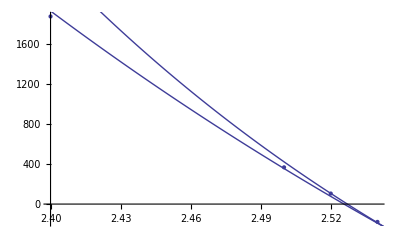

```mathematica
fitresS=FindFit[Transpose[{rs,Vs}][[1;;6]],AA+BB/r^4,{{AA,-7000},{BB,300000}},r]
Show[ListPlot[Transpose[{rs,Vs}][[3;;6]]],
Plot[AA+BB/r^4/.fitresS,{r,2.4,2.55}],Plot[-4452.5554+10711284/r^8.398,{r,2.4,2.55}]]
```

```mathematica
VsrS[r_]=-4452.5554+10711284/r^8.398;
UsrS[r_]=100*c(-4452.5554+10711284/r^8.398);
```

#### plot short and medium range

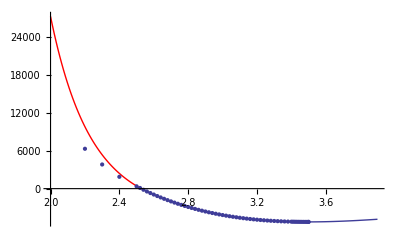

```mathematica
Show[Plot[VsrS[r],{r,2.0,2.53},PlotStyle->Red],
Plot[VmrS[r],{r,2.53,3.9}],
ListPlot[Transpose[{rs,Vs}]],
PlotRange->All]
```

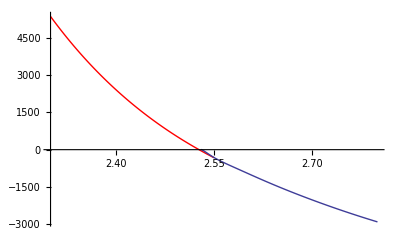

```mathematica
Show[Plot[VsrS[r],{r,2.3,2.55},PlotStyle->Red],
Plot[VmrS[r],{r,2.53,2.8}],
PlotRange->All]
```

take junction at 2.553 instead of 2.53 since that seems to match better
Note that Tiemann admitted that that was a typo.

#### long range

```mathematica
C6S=0.1179302*10^8;
C8S=0.3023023*10^9;
C10S=0.9843378*10^10;
AexS=0.1627150*10^4;
γS=5.25669;
βS=2.11445;
```

```mathematica
VlrS[r_]=-C6S/r^6-C8S/r^8-C10S/r^10-AexS*r^γS*Exp[-βS r];
UlrS[r_]=100*c VlrS[r];
```

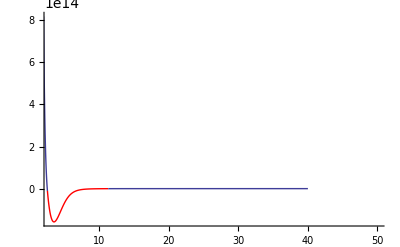

```mathematica
Show[Plot[UsrS[r],{r,2,2.553}],
Plot[UmrS[r],{r,2.553,11.3},PlotStyle->Red],
Plot[UlrS[r],{r,11.3,40},PlotRange->All],PlotRange->{{3,50},All}]
```

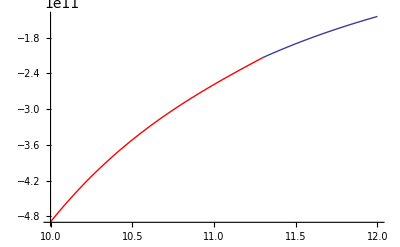

```mathematica
Show[
Plot[UmrS[r],{r,10,11.3},PlotStyle->Red],
Plot[UlrS[r],{r,11.3,12},PlotRange->All],PlotRange->{{10,12},All}]
```

```mathematica
UtotX1[r_]:=1/(100c)If[r<2.553,UsrS[r],If[r>11.3,UlrS[r],UmrS[r]]];
```

```mathematica
Graphics[{Directive[Thick,Red],Table[Line[{{RKRPotX1Na39K[[i,3]],RKRPotX1Na39K[[i,2]]},{RKRPotX1Na39K[[i,4]],RKRPotX1Na39K[[i,2]]}}],{i,1,Dimensions[RKRPotX1Na39K][[1]]}]},PlotRange->{{0,10},{0,5200}},AspectRatio->1]
```

Part::partw: Part 1 of {} does not exist.

Table::iterb: Iterator {i, 1, {} ⟦ 1 ⟧} does not have appropriate bounds.

Part::partw: Part 1 of {} does not exist.

Table::iterb: Iterator {i, 1, {} ⟦ 1 ⟧} does not have appropriate bounds.

-Graphics-

CompiledFunction::cfta: Argument YX1Na40K at position 1 should be a rank 2 tensor of "machine-size real number"s.

Part::partw: Part 1 of {} does not exist.

Part::pspec: Part specification 1 + k is neither an integer nor a list of integers.

Part::partw: Part 1 of {} does not exist.

Part::pspec: Part specification 1 + k is neither an integer nor a list of integers.

CompiledFunction::cfta: Argument YX1Na40K at position 1 should be a rank 2 tensor of "machine-size real number"s.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::pspec: Part specification 1 + k is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

CompiledFunction::cfta: Argument YX1Na40K at position 1 should be a rank 2 tensor of "machine-size real number"s.

General::stop: Further output of CompiledFunction :: cfta will be suppressed during this calculation.

NSum::nslim: Limit of summation -1. + {} ⟦ 1 ⟧ is not a number.

General::stop: Further output of NSum :: nslim will be suppressed during this calculation.

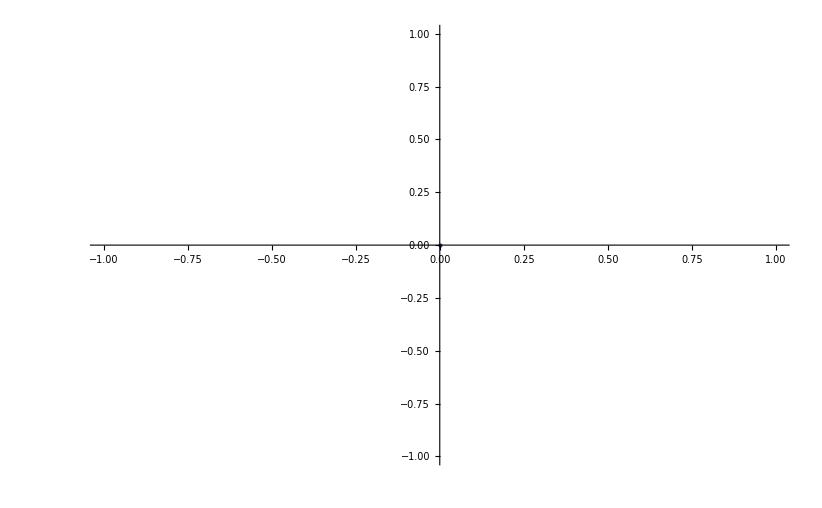

```mathematica
Show[ListPlot[Table[{J,Term[YX1Na40K,0,J]-Term[YX1Na40K,0,0]},{J,0,30}],PlotStyle->PointSize[Large],AxesStyle->Large],Graphics[{Directive[Thick,Blue],Line[{{0,74.3},{30,74.3}}]}]]
```

```mathematica
RKRPotX1Na39K[[i,3]]
```

Part::pspec: Part specification i is neither an integer nor a list of integers.

RKRPotX1Na39K⟦i,3⟧

```mathematica
Graphics[{Directive[Thick,Red],Table[Line[{{RKRPotX1Na39K[[i,3]],RKRPotX1Na39K[[i,2]]},{RKRPotX1Na39K[[i,4]],RKRPotX1Na39K[[i,2]]}}],{i,1,Dimensions[RKRPotX1Na39K][[1]]}]},PlotRange->{{2.2,5},{0,500}},AspectRatio->1]
```

Part::partw: Part 1 of {} does not exist.

Table::iterb: Iterator {i, 1, {} ⟦ 1 ⟧} does not have appropriate bounds.

-Graphics-

```mathematica
Show[Plot[UtotX1[r]+DeX,{r,2,15},PlotRange->{{2,15},{-20,5200}},Axes->False],Graphics[{Directive[Thick,Red],Table[Line[{{RKRPotX1Na39K[[i,3]],RKRPotX1Na39K[[i,2]]},{RKRPotX1Na39K[[i,4]],RKRPotX1Na39K[[i,2]]}}],{i,1,Dimensions[RKRPotX1Na39K][[1]]}]},PlotRange->{{2.2,5},{0,500}},AspectRatio->1],Graphics[{Directive[Thick,Red],Table[Line[{{RKRPotX1Na39K[[i,3]],RKRPotX1Na39K[[i,2]]},{RKRPotX1Na39K[[i,4]],RKRPotX1Na39K[[i,2]]}}],{i,1,Dimensions[RKRPotX1Na39K][[1]]}]},PlotRange->{{2.2,5},{0,500}},AspectRatio->1]]
```

Part::partw: Part 1 of {} does not exist.

Table::iterb: Iterator {i, 1, {} ⟦ 1 ⟧} does not have appropriate bounds.

Part::partw: Part 1 of {} does not exist.

Table::iterb: Iterator {i, 1, {} ⟦ 1 ⟧} does not have appropriate bounds.

General::stop: Further output of Table :: iterb will be suppressed during this calculation.

-Graphics-

```mathematica
Show[Plot[UtotX1[r]+DeX,{r,2.7,10},PlotRange->{{2.7,4.3},{-20,500}},Axes->False],Graphics[{Directive[Thick,Red],Table[Line[{{RKRPotX1Na39K[[i,3]],RKRPotX1Na39K[[i,2]]},{RKRPotX1Na39K[[i,4]],RKRPotX1Na39K[[i,2]]}}],{i,1,Dimensions[RKRPotX1Na39K][[1]]}]},PlotRange->{{2.2,5},{0,500}},AspectRatio->1],Graphics[{Directive[Thick,Red],Table[Line[{{RKRPotX1Na39K[[i,3]],RKRPotX1Na39K[[i,2]]},{RKRPotX1Na39K[[i,4]],RKRPotX1Na39K[[i,2]]}}],{i,1,Dimensions[RKRPotX1Na39K][[1]]}]},PlotRange->{{2.2,5},{0,500}},AspectRatio->1],Graphics[{Directive[Thick,Blue],Line[{{3.05,RKRPotX1Na39K[[1,2]]+ 74.3},{4,RKRPotX1Na39K[[1,2]]+74.3}}]},PlotRange->{{2.2,5},{0,500}},AspectRatio->1]]
```

Part::partw: Part 1 of {} does not exist.

Table::iterb: Iterator {i, 1, {} ⟦ 1 ⟧} does not have appropriate bounds.

Part::partw: Part 1 of {} does not exist.

Table::iterb: Iterator {i, 1, {} ⟦ 1 ⟧} does not have appropriate bounds.

General::stop: Further output of Table :: iterb will be suppressed during this calculation.

Part::partd: Part specification RKRPotX1Na39K ⟦ 1, 2 ⟧ is longer than depth of object.

-Graphics-

### Dunham coefficients of X1Σ+ state for Na^39 K Russier-Antoine et al., J. Phys. B: At. Mol. Opt. Phys. 33, 2753 (2000) http://iopscience.iop.org/0953-4075/33/14/312

```mathematica
mu = muNa39K;
TeX1=0;
vmaxX1=62;
Y=Table[0,{i,1,10},{j,1,5}];
Y[[All,All]]=0;
Y=({{-0.0242, 0.95229083 10^-1, -0.22514747 10^-6, 0.52399300 10^-12, -0.28530786 10^-17}, {124.00869, -0.44671511 10^-3, -0.69379810 10^-9, 0.46401290 10^-15, -0.23417169 10^-18}, {-0.48518740, -0.40119066 10^-5, -0.38450884 10^-9, 0.89297698 10^-15, 0.37965748 10^-19}, {-.32143996 10^-2, 0.36729987 10^-6, 0.67000514 10^-10, -0.93109347 10^-16, -0.39626221 10^-20}, {0.31299010 10^-3, -0.54647786 10^-7, -0.64846359 10^-11, 0.28480050 10^-17, 0.16621617 10^-21}, {-0.28723065 10^-4, 0.42699577 10^-8, 0.36911427 10^-12, -0.26731300 10^-17, -0.20577878 10^-23}, {0.16126212 10^-5, -0.21018754 10^-9, -0.13087875 10^-13, 0.62287532 10^-18, -0.92961944 10^-25}, {-0.60792476 10^-7, 0.66546163 10^-11, 0.29228842 10^-15, -0.62087407 10^-19, 0.36175686 10^-26}, {0.15455135 10^-8, -0.13577705 10^-12, -0.40139465 10^-17, 0.34243139 10^-20, .20473210 10^-26}, {-0.26202271 10^-10, 0.17245153 10^-14, 0.33230366 10^-19, -0.11566210 10^-21, -.33208635 10^-27}, {0.28401146 10^-12, -0.12404785 10^-16, -0.21707093 10^-21, 0.24468622 10^-23, 0.23016573 10^-28}, {-0.17819948 10^-14, 0.38567732 10^-19, 0.19607647 10^-23, -0.31442801 10^-25, -0.46234771 10^-30}, {0.49310577 10^-17, 0, -0.11413562 10^-25, 0.22286972 10^-27, -0.16267367 10^-31}, {0, 0, 0, -.66367690 10^-30, 0.10022499 10^-32}, {0, 0, 0, 0, -0.20583609 10^-34}, {0, 0, 0, 0, 0.19693909 10^-36}, {0, 0, 0, 0, -0.74212648 10^-39}});
YX1Na39K = Y;
YX1Na39K//MatrixForm
```

(-0.0242 | 0.0952291 | -2.25147×10^-7 | 5.23993×10^-13 | -2.85308×10^-18
124.009 | -0.000446715 | -6.93798×10^-10 | 4.64013×10^-16 | -2.34172×10^-19
-0.485187 | -4.01191×10^-6 | -3.84509×10^-10 | 8.92977×10^-16 | 3.79657×10^-20
-0.0032144 | 3.673×10^-7 | 6.70005×10^-11 | -9.31093×10^-17 | -3.96262×10^-21
0.00031299 | -5.46478×10^-8 | -6.48464×10^-12 | 2.84801×10^-18 | 1.66216×10^-22
-0.0000287231 | 4.26996×10^-9 | 3.69114×10^-13 | -2.67313×10^-18 | -2.05779×10^-24
1.61262×10^-6 | -2.10188×10^-10 | -1.30879×10^-14 | 6.22875×10^-19 | -9.29619×10^-26
-6.07925×10^-8 | 6.65462×10^-12 | 2.92288×10^-16 | -6.20874×10^-20 | 3.61757×10^-27
1.54551×10^-9 | -1.35777×10^-13 | -4.01395×10^-18 | 3.42431×10^-21 | 2.04732×10^-27
-2.62023×10^-11 | 1.72452×10^-15 | 3.32304×10^-20 | -1.15662×10^-22 | -3.32086×10^-28
2.84011×10^-13 | -1.24048×10^-17 | -2.17071×10^-22 | 2.44686×10^-24 | 2.30166×10^-29
-1.78199×10^-15 | 3.85677×10^-20 | 1.96076×10^-24 | -3.14428×10^-26 | -4.62348×10^-31
4.93106×10^-18 | 0 | -1.14136×10^-26 | 2.2287×10^-28 | -1.62674×10^-32
0 | 0 | 0 | -6.63677×10^-31 | 1.00225×10^-33
0 | 0 | 0 | 0 | -2.05836×10^-35
0 | 0 | 0 | 0 | 1.96939×10^-37
0 | 0 | 0 | 0 | -7.42126×10^-40)

### RKR Potential for X1Σ+:

CompiledFunction::cfsa: Argument 0.5  + v
 at position 1 should be a "machine-size real number".

General::stop: Further output of CompiledFunction :: cfsa will be suppressed during this calculation.

(0 | 61.8585 | 3.36713 | 3.64183
1 | 184.888 | 3.27678 | 3.75417
2 | 306.925 | 3.2174 | 3.8358
3 | 427.959 | 3.17076 | 3.90498
4 | 547.984 | 3.13155 | 3.967
5 | 666.99 | 3.09738 | 4.02427
6 | 784.972 | 3.06688 | 4.07815
7 | 901.921 | 3.03925 | 4.12949
8 | 1017.83 | 3.0139 | 4.17885
9 | 1132.69 | 2.99046 | 4.22665
10 | 1246.49 | 2.96861 | 4.2732
11 | 1359.22 | 2.94813 | 4.31874
12 | 1470.87 | 2.92886 | 4.36345
13 | 1581.44 | 2.91064 | 4.4075
14 | 1690.9 | 2.89337 | 4.45102
15 | 1799.24 | 2.87694 | 4.49412
16 | 1906.46 | 2.86128 | 4.53689
17 | 2012.53 | 2.84632 | 4.57943
18 | 2117.45 | 2.832 | 4.62181
19 | 2221.2 | 2.81827 | 4.6641
20 | 2323.76 | 2.8051 | 4.70638
21 | 2425.12 | 2.79243 | 4.74869
22 | 2525.26 | 2.78025 | 4.79112
23 | 2624.16 | 2.76851 | 4.8337
24 | 2721.81 | 2.7572 | 4.87651
25 | 2818.17 | 2.74629 | 4.9196
26 | 2913.24 | 2.73577 | 4.96302
27 | 3006.99 | 2.7256 | 5.00684
28 | 3099.4 | 2.71578 | 5.05111
29 | 3190.43 | 2.7063 | 5.09589
30 | 3280.08 | 2.69713 | 5.14125
31 | 3368.3 | 2.68827 | 5.18726
32 | 3455.08 | 2.6797 | 5.23397
33 | 3540.39 | 2.67141 | 5.28148
34 | 3624.18 | 2.66341 | 5.32985
35 | 3706.44 | 2.65567 | 5.37916
36 | 3787.13 | 2.64819 | 5.42952
37 | 3866.22 | 2.64096 | 5.48102
38 | 3943.66 | 2.63398 | 5.53376
39 | 4019.42 | 2.62724 | 5.58786
40 | 4093.47 | 2.62074 | 5.64346
41 | 4165.75 | 2.61447 | 5.7007
42 | 4236.23 | 2.60843 | 5.75972
43 | 4304.87 | 2.60261 | 5.82072
44 | 4371.6 | 2.59702 | 5.88388
45 | 4436.4 | 2.59165 | 5.94943
46 | 4499.19 | 2.58649 | 6.01762
47 | 4559.94 | 2.58154 | 6.08873
48 | 4618.59 | 2.57681 | 6.16309
49 | 4675.07 | 2.57229 | 6.24107
50 | 4729.34 | 2.56798 | 6.3231
51 | 4781.32 | 2.56388 | 6.40969
52 | 4830.97 | 2.55999 | 6.50143
53 | 4878.2 | 2.55631 | 6.59903
54 | 4922.97 | 2.55284 | 6.70333
55 | 4965.2 | 2.54959 | 6.81533
56 | 5004.83 | 2.54655 | 6.93629
57 | 5041.78 | 2.54374 | 7.06772
58 | 5076.01 | 2.54115 | 7.21153
59 | 5107.44 | 2.53877 | 7.37011
60 | 5136.04 | 2.53662 | 7.54655
61 | 5161.74 | 2.53468 | 7.74485
62 | 5184.54 | 2.53293 | 7.97034)

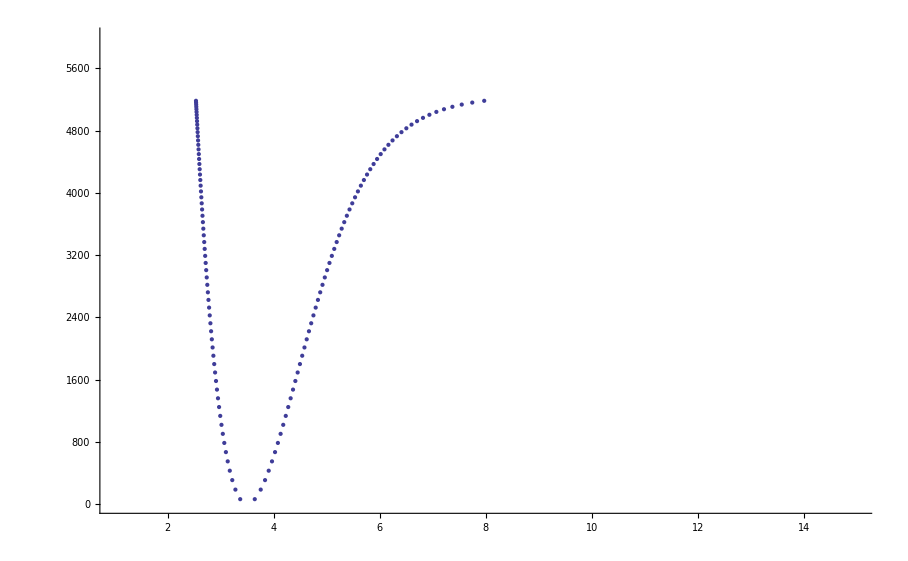

```mathematica
Y=YX1Na39K;
mu = muNa39K;
RKRPotX1Na39K = Table[{v,e[v],a[v],b[v]},{v,0,vmaxX1}];
BoundstatesX1Na39K = Table[{v,e[v]},{v,0,vmaxX1}];
RKRPotX1Na39K//MatrixForm
ShowX1Pot=Show[Plot[DeX+Utot[r],{r,2.5,40},PlotRange->All],ListPlot[Table[{RKRPotX1Na39K[[v,3]],RKRPotX1Na39K[[v,2]]},{v,1,vmaxX1+1}]],ListPlot[Table[{RKRPotX1Na39K[[v,4]],RKRPotX1Na39K[[v,2]]},{v,1,vmaxX1+1}]], PlotRange->{{1,15},{0,6000}}]
```

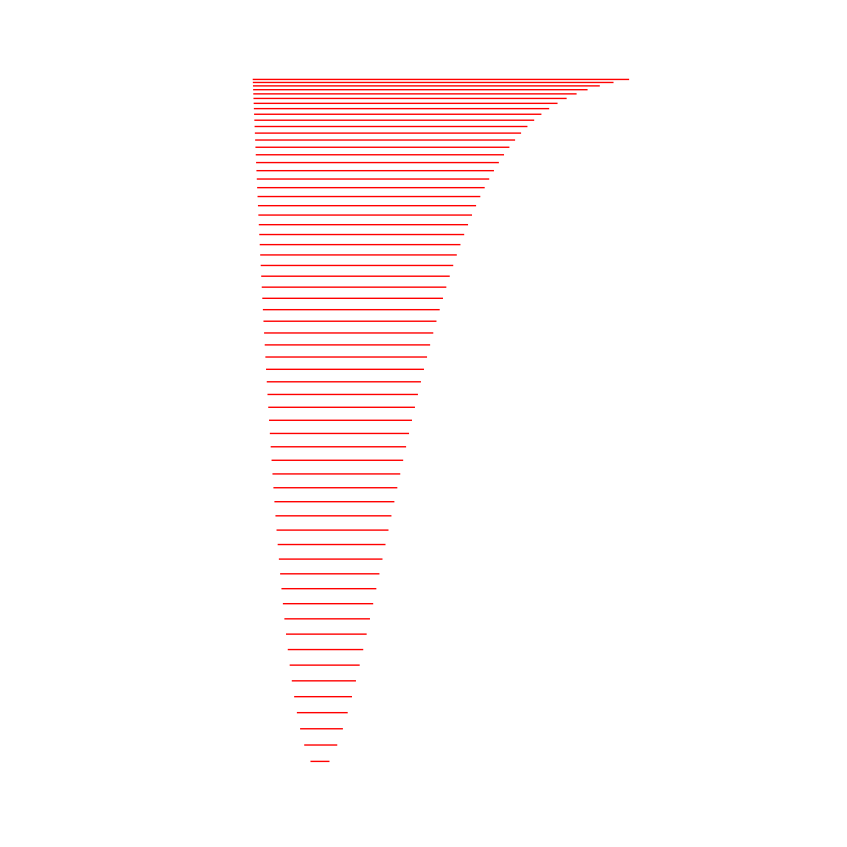

```mathematica
Graphics[{Directive[Thick,Red],Table[Line[{{RKRPotX1Na39K[[i,3]],RKRPotX1Na39K[[i,2]]},{RKRPotX1Na39K[[i,4]],RKRPotX1Na39K[[i,2]]}}],{i,1,Dimensions[RKRPotX1Na39K][[1]]}]},PlotRange->{{0,10},{0,5200}},AspectRatio->1]
```

### IPA Potential for X1Σ+:

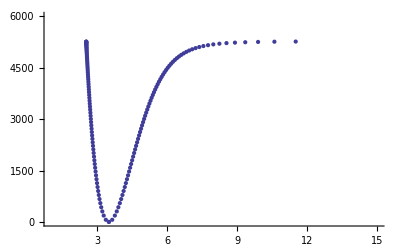

```mathematica
IPAPotX1Na39K =({{-0.5, -0.0245, 3.49904, 3.49904}, {0, 61.8578, 3.36716, 3.6418}, {1, 184.8878, 3.27679, 3.75415}, {2, 306.925, 3.21742, 3.83579}, {3, 427.9596, 3.17077, 3.90497}, {4, 547.9837, 3.13157, 3.96699}, {5, 666.99, 3.09739, 4.02426}, {6, 784.9715, 3.0669, 4.07814}, {7, 901.9206, 3.03926, 4.12948}, {8, 1017.8293, 3.01391, 4.17884}, {9, 1132.6889, 2.99046, 4.22664}, {10, 1246.4898, 2.96861, 4.27318}, {11, 1359.222, 2.94814, 4.31872}, {12, 1470.8747, 2.92887, 4.36343}, {13, 1581.4368, 2.91065, 4.40748}, {14, 1690.8964, 2.89338, 4.451}, {15, 1799.241, 2.87695, 4.4941}, {16, 1906.4577, 2.86129, 4.53687}, {17, 2012.5328, 2.84633, 4.57941}, {18, 2117.4521, 2.83201, 4.62179}, {19, 2221.2007, 2.81829, 4.66408}, {20, 2323.7628, 2.80511, 4.70635}, {21, 2425.1221, 2.79245, 4.74867}, {22, 2525.2614, 2.78026, 4.79109}, {23, 2624.1624, 2.76853, 4.83367}, {24, 2721.8063, 2.75722, 4.87648}, {25, 2818.173, 2.74631, 4.91956}, {26, 2913.2415, 2.73578, 4.96298}, {27, 3006.9899, 2.72562, 5.00679}, {28, 3099.3951, 2.7158, 5.05105}, {29, 3190.4328, 2.70631, 5.09583}, {30, 3280.0778, 2.69713, 5.14118}, {31, 3368.3035, 2.68826, 5.18718}, {32, 3455.0824, 2.67968, 5.23388}, {33, 3540.3856, 2.67139, 5.28137}, {34, 3624.1827, 2.66337, 5.32973}, {35, 3706.4423, 2.65562, 5.37903}, {36, 3787.1313, 2.64813, 5.42938}, {37, 3866.2152, 2.6409, 5.48086}, {38, 3943.6579, 2.63393, 5.53358}, {39, 4019.4214, 2.6272, 5.58767}, {40, 4093.4662, 2.6207, 5.64325}, {41, 4165.751, 2.61444, 5.70047}, {42, 4236.2323, 2.6084, 5.75948}, {43, 4304.865, 2.60256, 5.82046}, {44, 4371.6021, 2.59693, 5.88361}, {45, 4436.3944, 2.5915, 5.94914}, {46, 4499.1911, 2.58626, 6.01732}, {47, 4559.9391, 2.58123, 6.08841}, {48, 4618.5838, 2.57641, 6.16276}, {49, 4675.0682, 2.5718, 6.24073}, {50, 4729.3337, 2.56743, 6.32276}, {51, 4781.3198, 2.56329, 6.40935}, {52, 4830.964, 2.55941, 6.50109}, {53, 4878.2024, 2.55578, 6.59869}, {54, 4922.9698, 2.55241, 6.703}, {55, 4965.2001, 2.54928, 6.81502}, {56, 5004.827, 2.54641, 6.936}, {57, 5041.785, 2.54377, 7.06747}, {58, 5076.0107, 2.54137, 7.21131}, {59, 5107.4453, 2.53919, 7.36995}, {60, 5136.0363, 2.53723, 7.54645}, {61, 5161.742, 2.53546, 7.74484}, {62, 5184.5357, 2.5339, 7.97043}, {63, 5204.412, 2.53253, 8.23041}, {64, 5221.3948, 2.53135, 8.53472}, {65, 5235.5475, 2.53036, 8.89736}, {66, 5246.986, 2.52955, 9.33844}, {67, 5255.8912, 2.52892, 9.88727}, {68, 5262.5206, 2.52844, 10.58661}, {69, 5267.2077, 2.52811, 11.49863}, {70, 5272.2876, 2.52775, 14.41211}});
ShowIPAX1Pot=Show[Plot[DeX+Utot[r],{r,2.5,40},PlotRange->All],ListPlot[Table[{IPAPotX1Na39K[[v,3]],IPAPotX1Na39K[[v,2]]},{v,1,70+1}]],ListPlot[Table[{IPAPotX1Na39K[[v,4]],IPAPotX1Na39K[[v,2]]},{v,1,70+1}]], PlotRange->{{1,15},{0,6000}}]
```

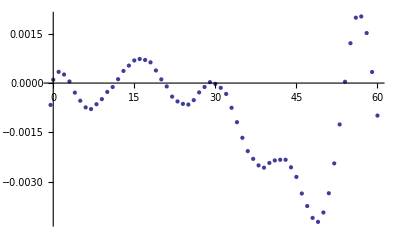

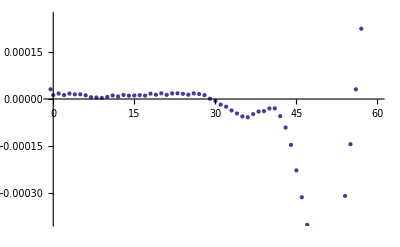

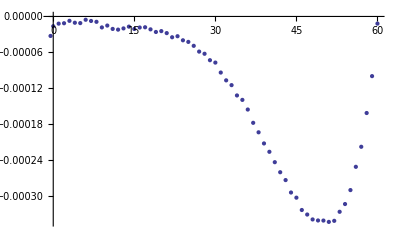

-Graphics-

-Graphics-

```mathematica
ListPlot[Table[{IPAPotX1Na39K[[v,1]],IPAPotX1Na39K[[v+1,2]]-RKRPotX1Na39K[[v,2]]},{v,1,vmaxX1}]]
ListPlot[Table[{IPAPotX1Na39K[[v,1]],IPAPotX1Na39K[[v+1,3]]-RKRPotX1Na39K[[v,3]]},{v,1,vmaxX1}]]
ListPlot[Table[{IPAPotX1Na39K[[v,1]],IPAPotX1Na39K[[v+1,4]]-RKRPotX1Na39K[[v,4]]},{v,1,vmaxX1}]]
ListPlot[Table[{IPAPotX1Na39K[[v,1]],IPAPotX1Na39K[[v,2]]-DeX-Utot[IPAPotX1Na39K[[v,3]]]},{v,1,71}]]
ListPlot[Table[{IPAPotX1Na39K[[v,1]],IPAPotX1Na39K[[v,2]]-DeX-Utot[IPAPotX1Na39K[[v,4]]]},{v,1,71}]]
```

### Finding energies of Na^40 K and Na^41 K X1Σ+ via mass scaling of Dunham coefficients: Dunham, Phys. Rev. 41, 721 (1932) http://prola.aps.org/abstract/PR/v41/i6/p721_1

#### Correction terms to simple mass scaling (essentially negligible for us...)

```mathematica
Y = YX1Na39K;
bc = Y;
bc[[All,All]]=0;
a1 = Y[[1+1,1+1]] Y[[1+1,0+1]]/(6 Y[[0+1,1+1]]^2)-1;
bc[[0+1,1+1]] = Y[[1+1,0+1]]^2 Y[[2+1,1+1]]/(4 Y[[0+1,1+1]]^3)+16 a1 Y[[2+1,0+1]]/(3Y[[0+1,1+1]])-8a1 - 6 a1^2+4 a1^3;
bc[[1+1,0+1]] = 5Y[[1+1,0+1]] Y[[3+1,0+1]]/(4 Y[[0+1,1+1]]^2)+a1 Y[[1+1,0+1]]^2 Y[[2+1,1+1]]/(3 Y[[0+1,1+1]]^3)-10 a1 -20 a1^2-15 a1^3/2-5 a1^4/2+Y[[2+1,0+1]](4 a1 + 16 a1^2/3)/Y[[0+1,1+1]]+Y[[2+1,0+1]]^2/(2 Y[[0+1,1+1]]^2);
bc[[0+1,2+1]] = 73/2+37a1 + 67 a1^2/2+33 a1^3-6 a1^4-9Y[[1+1,0+1]] Y[[3+1,0+1]]/(2 Y[[0+1,1+1]]^2)+Y[[1+1,0+1]]^2 Y[[2+1,1+1]](3-11a1/6)/(2 Y[[0+1,1+1]]^3)-Y[[2+1,0+1]](130/3+4a1+74 a1^2/3)/(2Y[[0+1,1+1]])+31 Y[[2+1,0+1]]^2/(9 Y[[0+1,1+1]]^2);
typicalcorrection = bc[[0+1,1+1]](YX1Na39K[[0+1,1+1]]/YX1Na39K[[1+1,0+1]])^2(muNa39K-muNa40K)/muNa40K
```

2.29532×10^-8

#### Do mass scaling for Na40K

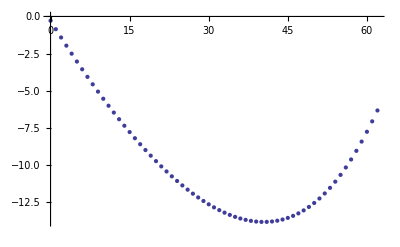

```mathematica
YX1Na40K = YX1Na39K;
For[i=1,i<Dimensions[YX1Na39K][[1]],i++,
For[j=0,j<Dimensions[YX1Na39K][[2]],j++,
YX1Na40K[[i+1,j+1]]=YX1Na39K[[i+1,j+1]](muNa39K/muNa40K)^((i+2j)/2)(1+bc[[i+1,j+1]](YX1Na39K[[0+1,1+1]]/YX1Na39K[[1+1,0+1]])^2(muNa39K-muNa40K)/muNa40K)
]]
Y=YX1Na40K;
mu = muNa40K;
BoundstatesX1Na40K = Table[{v,e[v]},{v,0,vmaxX1}];
IsotopeshiftX1Na40K = Table[{v,BoundstatesX1Na40K[[v+1,2]]-BoundstatesX1Na39K[[v+1,2]]},{v,0,vmaxX1}];
ListPlot[IsotopeshiftX1Na40K]
```

#### Do mass scaling for Na41K

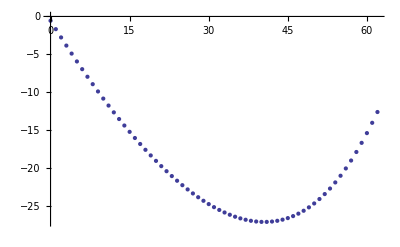

```mathematica
YX1Na41K = YX1Na39K;
For[i=1,i<Dimensions[YX1Na39K][[1]],i++,
For[j=0,j<Dimensions[YX1Na39K][[2]],j++,
YX1Na41K[[i+1,j+1]]=YX1Na39K[[i+1,j+1]](muNa39K/muNa41K)^((i+2j)/2)(1+bc[[i+1,j+1]](YX1Na39K[[0+1,1+1]]/YX1Na39K[[1+1,0+1]])^2(muNa39K-muNa41K)/muNa41K)
]]
Y=YX1Na41K;
mu = muNa41K;
BoundstatesX1Na41K = Table[{v,e[v]},{v,0,vmaxX1}];
IsotopeshiftX1Na41K = Table[{v,BoundstatesX1Na41K[[v+1,2]]-BoundstatesX1Na39K[[v+1,2]]},{v,0,vmaxX1}];
ListPlot[IsotopeshiftX1Na41K]
```

```mathematica
Term[YX1Na40K,0,0]-DeX
```

-5212.05

```mathematica
-Term[YX1Na39K,0,0]
```

-61.8585

## a3Σ+

### Potential definition from Gerdes,..., Tiemann, Eur. Phys. J. D 49, 67–73 (2008)

#### short range

```mathematica
A=-0.6838392*10^3;
B=+0.281763541*10^6;
q=4;
```

```mathematica
VsrT[r_]=A+B/r^q ;
UsrT[r_]=100*c(A+B/r^q);
```

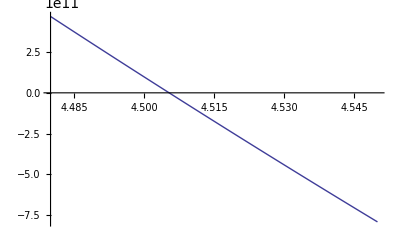

```mathematica
Plot[UsrT[r],{r,4.48,4.55}]
```

#### medium range

```mathematica
aT=Table[0,{i,16}];
```

```mathematica
bT= -0.66;
RmT= 5.47298825;
Dea3= 207.7495;
aT[[1]]=-207.7495;
aT[[2]]= 0.104345*10^2;
aT[[3]] =0.3811560*10^3;
aT[[4]]= 0.2432236*10^3;
aT[[5]]= 0.182422*10^2;
aT[[6]] =-0.1183588*10^3;
aT[[7]] =-0.5243827*10^3;
aT[[8]] =-0.7362683*10^3;
aT[[9]]= 0.12436734*10^4;
aT[[10]]=0.13720076*10^4;
aT[[11]]= -0.40511451*10^4;
aT[[12]] =-0.25977888*10^4;
aT[[13]] =0.59928116*10^4;
aT[[14]] =0.37710157*10^4;
aT[[15]]= -0.29764114*10^4;
aT[[16]]= -0.20459436*10^4;
```

```mathematica
VmrT[r_]=Sum[aT[[p]]*((r-RmT)/(r+bT RmT))^(p-1),{p,1,16}];
UmrT[r_]=100*c VmrT[r];
```

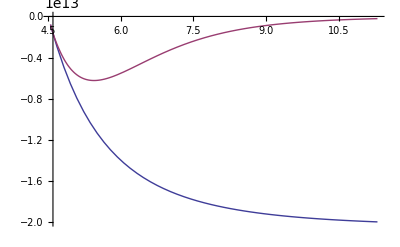

```mathematica
Plot[{UsrT[r],UmrT[r]},{r,4.55,11.3}]
```

#### long range

```mathematica
C6T=0.1179302*10^8;
C8T=0.3023023*10^9;
C10T=0.9843378*10^10;
AexT=0.1627150*10^4;
γT=5.25669;
βT=2.11445;
```

```mathematica
VlrT[r_]=-C6T/r^6-C8T/r^8-C10T/r^10+AexT*r^γT*Exp[-βT r];
UlrT[r_]=100*c VlrT[r];
```

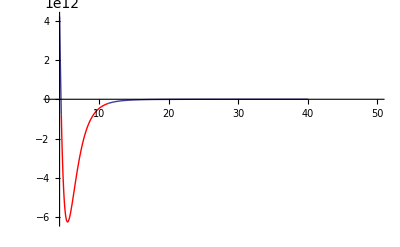

```mathematica
Show[Plot[UsrT[r],{r,4.3,4.55}],
Plot[UmrT[r],{r,4.55,11.3},PlotStyle->Red],
Plot[UlrT[r],{r,11.3,40},PlotRange->All],PlotRange->{{3,50},All}]
```

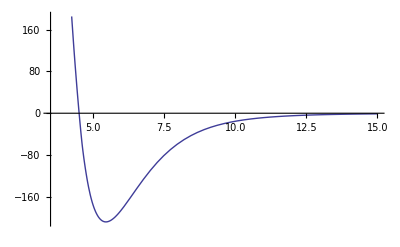

```mathematica
Utota3[r_]:=1/(100c)If[r<4.55,UsrT[r],If[r>11.3,UlrT[r],UmrT[r]]];
Plot[Utota3[r],{r,3.5,15}]
```

### Dunham coefficients of a3Σ+ state for Na^39 K Gerdes,..., Tiemann, Eur. Phys. J. D 49, 67–73 (2008)

```mathematica
mu = muNa39K;
vmaxa3 = 18;
Y=Table[0,{i,1,10},{j,1,3}];
Y[[All,All]]=0;
Y=({{0, 0.0393984, -0.51470 10^-6, 0, 0}, {23.0099, -0.125123 10^-2, 0, 0, 0}, {-0.62169, 0.197 10^-5, 0, -0.2588 10^-11, -0.3962 10^-16}, {0, -0.18082 10^-5, -0.1835 10^-8, 0.8593 10^-12, 0}, {-0.2627 10^-3, 0, 0.1682 10^-9, -0.6040 10^-13, 0}, {0.2528 10^-4, 0, 0, 0, 0}, {-0.1623 10^-5, 0, -0.3502 10^-12, 0, 0}, {0.4811 10^-7, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}});
Ya3Na39K = Y;
```

### RKR Potential for a3Σ+:

CompiledFunction::cfsa: Argument 0.5  + v
 at position 1 should be a "machine-size real number".

General::stop: Further output of CompiledFunction :: cfsa will be suppressed during this calculation.

(0 | 11.3495 | 5.15647 | 5.80044
1 | 33.1149 | 4.98708 | 6.12921
2 | 53.631 | 4.8861 | 6.39797
3 | 72.8901 | 4.81245 | 6.64954
4 | 90.8826 | 4.75454 | 6.89762
5 | 107.598 | 4.70726 | 7.14985
6 | 123.024 | 4.66787 | 7.41207
7 | 137.148 | 4.63474 | 7.68976
8 | 149.96 | 4.60682 | 7.98895
9 | 161.446 | 4.58336 | 8.31685
10 | 171.598 | 4.5638 | 8.68279
11 | 180.411 | 4.54768 | 9.09943
12 | 187.889 | 4.53453 | 9.58485
13 | 194.048 | 4.52391 | 10.1662
14 | 198.924 | 4.51533 | 10.8865
15 | 202.581 | 4.50835 | 11.8192
16 | 205.122 | 4.503 | 13.1001
17 | 206.7 | 4.50179 | 15.0068
18 | 207.536 | 4.52262 | 18.1187)

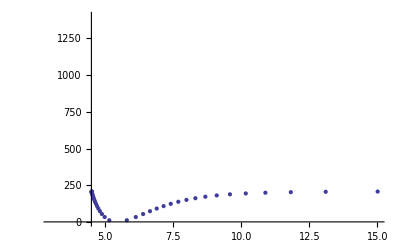

```mathematica
Y=Ya3Na39K;
mu = muNa39K;
RKRPota3Na39K = Table[{v,e[v],a[v],b[v]},{v,0,vmaxa3}];
Boundstatesa3Na39K = Table[{v,e[v]},{v,0,vmaxa3}];
RKRPota3Na39K//MatrixForm
Showa3Pot=Show[ListPlot[Table[{RKRPota3Na39K[[v,3]],RKRPota3Na39K[[v,2]]},{v,1,vmaxa3+1}]],ListPlot[Table[{RKRPota3Na39K[[v,4]],RKRPota3Na39K[[v,2]]},{v,1,vmaxa3+1}]], PlotRange->{{3,15},{0,1400}}]
```

### Finding energies of Na^40 K and Na^41 K a3Σ+ via mass scaling of Dunham coefficients: Dunham, Phys. Rev. 41, 721 (1932) http://prola.aps.org/abstract/PR/v41/i6/p721_1

#### Correction terms to simple mass scaling (essentially negligible for us...)

```mathematica
Y = Ya3Na39K;
bc = Y;
bc[[All,All]]=0;
a1 = Y[[1+1,1+1]] Y[[1+1,0+1]]/(6 Y[[0+1,1+1]]^2)-1;
bc[[0+1,1+1]] = Y[[1+1,0+1]]^2 Y[[2+1,1+1]]/(4 Y[[0+1,1+1]]^3)+16 a1 Y[[2+1,0+1]]/(3Y[[0+1,1+1]])-8a1 - 6 a1^2+4 a1^3;
bc[[1+1,0+1]] = 5Y[[1+1,0+1]] Y[[3+1,0+1]]/(4 Y[[0+1,1+1]]^2)+a1 Y[[1+1,0+1]]^2 Y[[2+1,1+1]]/(3 Y[[0+1,1+1]]^3)-10 a1 -20 a1^2-15 a1^3/2-5 a1^4/2+Y[[2+1,0+1]](4 a1 + 16 a1^2/3)/Y[[0+1,1+1]]+Y[[2+1,0+1]]^2/(2 Y[[0+1,1+1]]^2);
bc[[0+1,2+1]] = 73/2+37a1 + 67 a1^2/2+33 a1^3-6 a1^4-9Y[[1+1,0+1]] Y[[3+1,0+1]]/(2 Y[[0+1,1+1]]^2)+Y[[1+1,0+1]]^2 Y[[2+1,1+1]](3-11a1/6)/(2 Y[[0+1,1+1]]^3)-Y[[2+1,0+1]](130/3+4a1+74 a1^2/3)/(2Y[[0+1,1+1]])+31 Y[[2+1,0+1]]^2/(9 Y[[0+1,1+1]]^2);
typicalcorrection = bc[[0+1,1+1]](Ya3Na39K[[0+1,1+1]]/Ya3Na39K[[1+1,0+1]])^2(muNa39K-muNa40K)/muNa40K
```

-1.89006×10^-7

#### Do mass scaling for Na40K

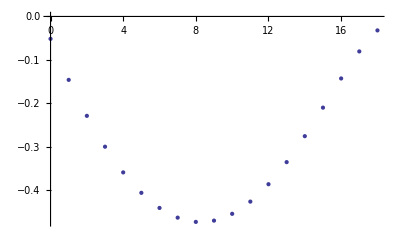

```mathematica
Ya3Na40K = Ya3Na39K;
For[i=1,i<Dimensions[Ya3Na39K][[1]],i++,
For[j=0,j<Dimensions[Ya3Na39K][[2]],j++,
Ya3Na40K[[i+1,j+1]]=Ya3Na39K[[i+1,j+1]](muNa39K/muNa40K)^((i+2j)/2)(1+bc[[i+1,j+1]](Ya3Na39K[[0+1,1+1]]/Ya3Na39K[[1+1,0+1]])^2(muNa39K-muNa40K)/muNa40K)
]]
Y=Ya3Na40K;
mu = muNa40K;
Boundstatesa3Na40K = Table[{v,e[v]},{v,0,vmaxa3}];
Isotopeshifta3Na40K = Table[{v,Boundstatesa3Na40K[[v+1,2]]-Boundstatesa3Na39K[[v+1,2]]},{v,0,vmaxa3}];
ListPlot[Isotopeshifta3Na40K]
```

#### Do mass scaling for Na41K

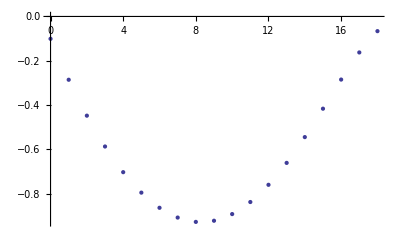

```mathematica
Ya3Na41K = Ya3Na39K;
For[i=1,i<Dimensions[Ya3Na39K][[1]],i++,
For[j=0,j<Dimensions[Ya3Na39K][[2]],j++,
Ya3Na41K[[i+1,j+1]]=Ya3Na39K[[i+1,j+1]](muNa39K/muNa41K)^((i+2j)/2)(1+bc[[i+1,j+1]](Ya3Na39K[[0+1,1+1]]/Ya3Na39K[[1+1,0+1]])^2(muNa39K-muNa41K)/muNa41K)
]]
Y=Ya3Na41K;
mu = muNa41K;
Boundstatesa3Na41K = Table[{v,e[v]},{v,0,vmaxa3}];
Isotopeshifta3Na41K = Table[{v,Boundstatesa3Na41K[[v+1,2]]-Boundstatesa3Na39K[[v+1,2]]},{v,0,vmaxa3}];
ListPlot[Isotopeshifta3Na41K]
```

## B1Π

### Dunham coefficients of B1Π state for Na^39 K Kasahara, Baba, Kato, J. Chem. Phys. 94, 7713 (1991) http://dx.doi.org/10.1063/1.460157

```mathematica
mu = muNa39K;
TeB1Pi = 16992.7446;
vmaxB1Pi = 43;
Y=Table[0,{i,1,10},{j,1,3}];
Y[[All,All]]=0;
Y[[0+1,0+1]]=-0.0430;
Y[[1+1,0+1]]=71.4630;
Y[[2+1,0+1]]=-1.15092;
Y[[3+1,0+1]]=-1.0613 10^-2;
Y[[4+1,0+1]]=9.9950 10^-4;
Y[[5+1,0+1]]=-1.42656 10^-5;
Y[[6+1,0+1]]=-8.67783 10^-7;
Y[[7+1,0+1]]=4.74996 10^-8;
Y[[8+1,0+1]]=-9.30786 10^-10;
Y[[9+1,0+1]]=6.67343 10^-12;
Y[[0+1,1+1]]=7.23853 10^-2;
Y[[1+1,1+1]]=-1.17799 10^-3;
Y[[2+1,1+1]]=-1.3502 10^-5;
Y[[3+1,1+1]]=-4.7933 10^-7;
Y[[4+1,1+1]]=4.82977 10^-8;
Y[[5+1,1+1]]=-6.88606 10^-10;
Y[[6+1,1+1]]=-1.13984 10^-11;
Y[[7+1,1+1]]=2.09534 10^-13;
Y[[0+1,2+1]]=-2.89859 10^-7;
Y[[1+1,2+1]]=-1.93901 10^-8;
Y[[2+1,2+1]]=6.45399 10^-10;
Y[[3+1,2+1]]=-7.75355 10^-12;
Y[[4+1,2+1]]=9.91847 10^-13;
Y[[5+1,2+1]]=-3.46351 10^-14;
YB1PiNa39K = Y;
Y//MatrixForm
```

(-0.043 | 0.0723853 | -2.89859×10^-7
71.463 | -0.00117799 | -1.93901×10^-8
-1.15092 | -0.000013502 | 6.45399×10^-10
-0.010613 | -4.7933×10^-7 | -7.75355×10^-12
0.0009995 | 4.82977×10^-8 | 9.91847×10^-13
-0.0000142656 | -6.88606×10^-10 | -3.46351×10^-14
-8.67783×10^-7 | -1.13984×10^-11 | 0
4.74996×10^-8 | 2.09534×10^-13 | 0
-9.30786×10^-10 | 0 | 0
6.67343×10^-12 | 0 | 0)

```mathematica
BoundstatesB1PiNa39K[[17]]
```

Part::partd: Part specification BoundstatesB1PiNa39K ⟦ 17 ⟧ is longer than depth of object.

BoundstatesB1PiNa39K⟦17⟧

### RKR Potential for B1Π:

CompiledFunction::cfsa: Argument 0.5  + v
 at position 1 should be a "machine-size real number".

General::stop: Further output of CompiledFunction :: cfsa will be suppressed during this calculation.

(0 | 35.3995 | 3.84659 | 4.21033
1 | 104.531 | 3.74007 | 4.37903
2 | 171.293 | 3.67338 | 4.51049
3 | 235.665 | 3.62286 | 4.62857
4 | 297.645 | 3.58172 | 4.74021
5 | 357.248 | 3.54691 | 4.84862
6 | 414.499 | 3.51677 | 4.9556
7 | 469.437 | 3.49026 | 5.06231
8 | 522.106 | 3.46671 | 5.16955
9 | 572.559 | 3.44561 | 5.2779
10 | 620.85 | 3.42662 | 5.38782
11 | 667.038 | 3.40945 | 5.49967
12 | 711.183 | 3.39388 | 5.61378
13 | 753.343 | 3.37973 | 5.73041
14 | 793.58 | 3.36682 | 5.84983
15 | 831.951 | 3.35503 | 5.97228
16 | 868.516 | 3.34422 | 6.09801
17 | 903.329 | 3.33431 | 6.22726
18 | 936.448 | 3.32519 | 6.36028
19 | 967.925 | 3.31678 | 6.49736
20 | 997.814 | 3.30901 | 6.63877
21 | 1026.17 | 3.30184 | 6.78486
22 | 1053.03 | 3.29522 | 6.93597
23 | 1078.45 | 3.28913 | 7.09255
24 | 1102.48 | 3.28354 | 7.25509
25 | 1125.15 | 3.27845 | 7.4242
26 | 1146.5 | 3.27387 | 7.60062
27 | 1166.57 | 3.26981 | 7.78529
28 | 1185.38 | 3.26626 | 7.97941
29 | 1202.95 | 3.26325 | 8.18448
30 | 1219.3 | 3.26077 | 8.40249
31 | 1234.42 | 3.25879 | 8.63601
32 | 1248.33 | 3.2573 | 8.8884
33 | 1261.01 | 3.25623 | 9.16413
34 | 1272.45 | 3.25551 | 9.46915
35 | 1282.64 | 3.25501 | 9.81146
36 | 1291.56 | 3.25461 | 10.202
37 | 1299.21 | 3.2542 | 10.6558
38 | 1305.62 | 3.25373 | 11.1936
39 | 1310.82 | 3.25347 | 11.8436
40 | 1314.9 | 3.25448 | 12.6402
41 | 1318.02 | 3.26006 | 13.6101
42 | 1320.41 | 3.27858 | 14.712
43 | 1322.43 | 3.32532 | 15.7067)

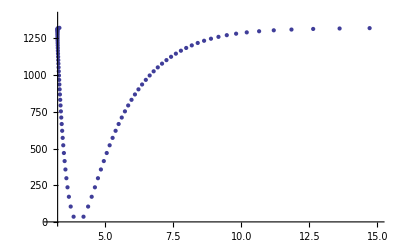

```mathematica
Y=YB1PiNa39K;
mu = muNa39K;
RKRPotB1PiNa39K = Table[{v,e[v],a[v],b[v]},{v,0,43}];
BoundstatesB1PiNa39K = Table[{v,e[v]},{v,0,43}];
RKRPotB1PiNa39K//MatrixForm
ShowB1PiPot=Show[ListPlot[Table[{RKRPotB1PiNa39K[[v,3]],RKRPotB1PiNa39K[[v,2]]},{v,1,44}]],ListPlot[Table[{RKRPotB1PiNa39K[[v,4]],RKRPotB1PiNa39K[[v,2]]},{v,1,44}]], PlotRange->{{3,15},{0,1400}}]
```

### Fixing the issue of backbending of the RKR potential:

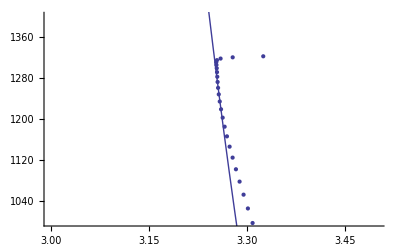

```mathematica
Vcorr[x_]:=3.85547 10^9/x^12-1450.79;(* Fitted form of potential from Kato *)
Show[ListPlot[Table[{RKRPotB1PiNa39K[[v,3]],RKRPotB1PiNa39K[[v,2]]},{v,1,44}]],ListPlot[Table[{RKRPotB1PiNa39K[[v,4]],RKRPotB1PiNa39K[[v,2]]},{v,1,44}]],Plot[Vcorr[x],{x,3.2,3.6}],PlotRange->{{3,3.5},{1000,1400}}]
```

(0 | 35.3995 | 3.84659 | 4.21033
1 | 104.531 | 3.74007 | 4.37903
2 | 171.293 | 3.67338 | 4.51049
3 | 235.665 | 3.62286 | 4.62857
4 | 297.645 | 3.58172 | 4.74021
5 | 357.248 | 3.54691 | 4.84862
6 | 414.499 | 3.51677 | 4.9556
7 | 469.437 | 3.49026 | 5.06231
8 | 522.106 | 3.46671 | 5.16955
9 | 572.559 | 3.44561 | 5.2779
10 | 620.85 | 3.42662 | 5.38782
11 | 667.038 | 3.40945 | 5.49967
12 | 711.183 | 3.39388 | 5.61378
13 | 753.343 | 3.37973 | 5.73041
14 | 793.58 | 3.36682 | 5.84983
15 | 831.951 | 3.35503 | 5.97228
16 | 868.516 | 3.34422 | 6.09801
17 | 903.329 | 3.33431 | 6.22726
18 | 936.448 | 3.32519 | 6.36028
19 | 967.925 | 3.31678 | 6.49736
20 | 997.814 | 3.30901 | 6.63877
21 | 1026.17 | 3.30184 | 6.78486
22 | 1053.03 | 3.29522 | 6.93597
23 | 1078.45 | 3.28913 | 7.09255
24 | 1102.48 | 3.28354 | 7.25509
25 | 1125.15 | 3.27845 | 7.4242
26 | 1146.5 | 3.27387 | 7.60062
27 | 1166.57 | 3.26981 | 7.78529
28 | 1185.38 | 3.26626 | 7.97941
29 | 1202.95 | 3.26325 | 8.18448
30 | 1219.3 | 3.26077 | 8.40249
31 | 1234.42 | 3.25879 | 8.63601
32 | 1248.33 | 3.2573 | 8.8884
33 | 1261.01 | 3.25623 | 9.16413
34 | 1272.45 | 3.25551 | 9.46915
35 | 1282.64 | 3.25422 | 9.81068
36 | 1291.56 | 3.25334 | 10.2007
37 | 1299.21 | 3.25259 | 10.6542
38 | 1305.62 | 3.25195 | 11.1918
39 | 1310.82 | 3.25144 | 11.8416
40 | 1314.9 | 3.25104 | 12.6368
41 | 1318.02 | 3.25074 | 13.6008
42 | 1320.41 | 3.2505 | 14.684
43 | 1322.43 | 3.25031 | 15.6317)

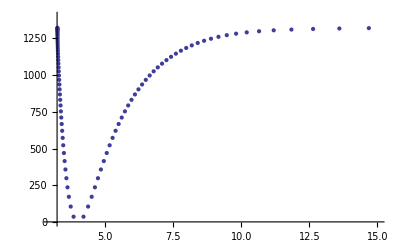

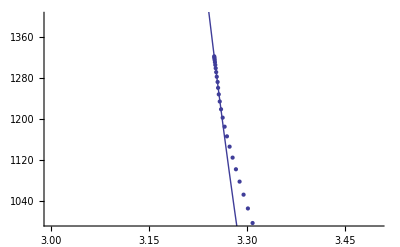

```mathematica
RKRPotB1PiNaK39corr =RKRPotB1PiNa39K;
For[i=35,i<44,i+=1;
RKRPotB1PiNaK39corr[[i,3]]=x/.FindRoot[Vcorr[x]==RKRPotB1PiNa39K[[i,2]],{x,3}];
RKRPotB1PiNaK39corr[[i,4]]=RKRPotB1PiNa39K[[i,4]]-RKRPotB1PiNa39K[[i,3]]+x/.FindRoot[Vcorr[x]==RKRPotB1PiNa39K[[i,2]],{x,3}]
]
RKRPotB1PiNaK39corr//MatrixForm
ShowB1PiPot =Show[ListPlot[Table[{RKRPotB1PiNaK39corr[[v,3]],RKRPotB1PiNaK39corr[[v,2]]},{v,1,44}]],ListPlot[Table[{RKRPotB1PiNaK39corr[[v,4]],RKRPotB1PiNaK39corr[[v,2]]},{v,1,44}]], PlotRange->{{3,15},{0,1400}}]
Show[ListPlot[Table[{RKRPotB1PiNaK39corr[[v,3]],RKRPotB1PiNaK39corr[[v,2]]},{v,1,44}]],ListPlot[Table[{RKRPotB1PiNaK39corr[[v,4]],RKRPotB1PiNaK39corr[[v,2]]},{v,1,44}]],Plot[Vcorr[x],{x,3.2,3.6}],PlotRange->{{3,3.5},{1000,1400}}]
```

### Finding energies of Na^40 K and Na^41 K B1Π via mass scaling of Dunham coefficients: Dunham, Phys. Rev. 41, 721 (1932) http://prola.aps.org/abstract/PR/v41/i6/p721_1

#### Correction terms to simple mass scaling (essentially negligible for us...)

```mathematica
Y = YB1PiNa39K;
bc = Y;
bc[[All,All]]=0;
a1 = Y[[1+1,1+1]] Y[[1+1,0+1]]/(6 Y[[0+1,1+1]]^2)-1;
bc[[0+1,1+1]] = Y[[1+1,0+1]]^2 Y[[2+1,1+1]]/(4 Y[[0+1,1+1]]^3)+16 a1 Y[[2+1,0+1]]/(3Y[[0+1,1+1]])-8a1 - 6 a1^2+4 a1^3;
bc[[1+1,0+1]] = 5Y[[1+1,0+1]] Y[[3+1,0+1]]/(4 Y[[0+1,1+1]]^2)+a1 Y[[1+1,0+1]]^2 Y[[2+1,1+1]]/(3 Y[[0+1,1+1]]^3)-10 a1 -20 a1^2-15 a1^3/2-5 a1^4/2+Y[[2+1,0+1]](4 a1 + 16 a1^2/3)/Y[[0+1,1+1]]+Y[[2+1,0+1]]^2/(2 Y[[0+1,1+1]]^2);
bc[[0+1,2+1]] = 73/2+37a1 + 67 a1^2/2+33 a1^3-6 a1^4-9Y[[1+1,0+1]] Y[[3+1,0+1]]/(2 Y[[0+1,1+1]]^2)+Y[[1+1,0+1]]^2 Y[[2+1,1+1]](3-11a1/6)/(2 Y[[0+1,1+1]]^3)-Y[[2+1,0+1]](130/3+4a1+74 a1^2/3)/(2Y[[0+1,1+1]])+31 Y[[2+1,0+1]]^2/(9 Y[[0+1,1+1]]^2);
typicalcorrection = bc[[0+1,1+1]](YB1PiNa39K[[0+1,1+1]]/YB1PiNa39K[[1+1,0+1]])^2(muNa39K-muNa40K)/muNa40K
```

-1.49683×10^-7

#### Do mass scaling for Na40K

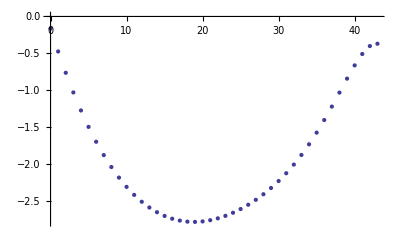

```mathematica
YB1PiNa40K = YB1PiNa39K;
For[i=1,i<10,i++,
For[j=0,j<3,j++,
YB1PiNa40K[[i+1,j+1]]=YB1PiNa39K[[i+1,j+1]](muNa39K/muNa40K)^((i+2j)/2)(1+bc[[i+1,j+1]](YB1PiNa39K[[0+1,1+1]]/YB1PiNa39K[[1+1,0+1]])^2(muNa39K-muNa40K)/muNa40K)
]]
Y=YB1PiNa40K;
mu = muNa40K;
BoundstatesB1PiNa40K = Table[{v,e[v]},{v,0,43}];
IsotopeshiftB1Pi = Table[{v,BoundstatesB1PiNa40K[[v+1,2]]-BoundstatesB1PiNa39K[[v+1,2]]},{v,0,43}];
PAlinesB1PiNa40K =Table[{v,TeB1Pi - YB1PiNa40K[[1,1]]- DeX+BoundstatesB1PiNa40K[[v+1,2]]},{v,0,43}];
PAwavelengthB1PiNa40K = Table[{v,1/100/PAlinesB1PiNa40K[[v+1,2]] 10^9},{v,0,43}];
ListPlot[IsotopeshiftB1Pi]
```

#### Do mass scaling for Na41K

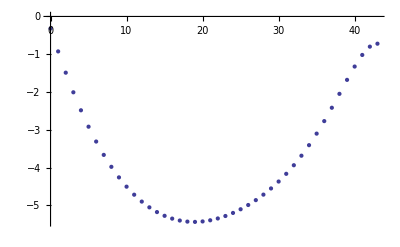

```mathematica
YB1PiNa41K = YB1PiNa39K;
For[i=1,i<10,i++,
For[j=0,j<3,j++,
YB1PiNa41K[[i+1,j+1]]=YB1PiNa39K[[i+1,j+1]](muNa39K/muNa41K)^((i+2j)/2)(1+bc[[i+1,j+1]](YB1PiNa39K[[0+1,1+1]]/YB1PiNa39K[[1+1,0+1]])^2(muNa39K-muNa41K)/muNa41K)
]]
Y=YB1PiNa41K;
mu = muNa41K;
BoundstatesB1PiNa41K = Table[{v,e[v]},{v,0,43}];
IsotopeshiftB1Pi39K41K = Table[{v,BoundstatesB1PiNa41K[[v+1,2]]-BoundstatesB1PiNa39K[[v+1,2]]},{v,0,43}];
PAlinesB1PiNa41K =Table[{v,TeB1Pi - YB1PiNa40K[[1,1]]- DeX+BoundstatesB1PiNa41K[[v+1,2]]},{v,0,43}];
PAwavelengthB1PiNa41K = Table[{v,1/100/PAlinesB1PiNa41K[[v+1,2]] 10^9},{v,0,43}];
ListPlot[IsotopeshiftB1Pi39K41K]
```

## c3Σ +

### Dunham coefficients of c3Σ+ state for Na^39 K R. Ferber et al., J. Chem. Phys. 112, 5740 (2000) http://dx.doi.org/10.1063/1.481149

```mathematica
mu = muNa39K;
Tec3sigmaplus = 15750.64;
vmaxc3SigmaPlus =50;
Y=Table[0,{i,1,10},{j,1,3}];
Y[[All,All]]=0;
Y[[0+1,0+1]]=0;
Y[[1+1,0+1]]=73.4;
Y[[2+1,0+1]]=-0.480173;
Y[[3+1,0+1]]=-9.82485 10^-4;
Y[[0+1,1+1]]=0.06275;
Y[[1+1,1+1]]=-5.91425 10^-4;
Y[[2+1,1+1]]=-1.81058 10^-6;
Y[[0+1,2+1]]=1.83 10^-7;
Y[[1+1,2+1]]=3.45 10^-9;
Y[[2+1,2+1]]=-2.17 10^-11;
Yc3SigmaPlusNa39K = Y;
Y//MatrixForm
```

(0 | 0.06275 | 1.83×10^-7
73.4 | -0.000591425 | 3.45×10^-9
-0.480173 | -1.81058×10^-6 | -2.17×10^-11
-0.000982485 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

### RKR Potential for c3Σ+:

CompiledFunction::cfsa: Argument 0.5  + v
 at position 1 should be a "machine-size real number".

General::stop: Further output of CompiledFunction :: cfsa will be suppressed during this calculation.

(0 | 36.5798 | 4.14226 | 4.49971
1 | 109.016 | 4.03093 | 4.6535
2 | 180.484 | 3.95962 | 4.7679
3 | 250.976 | 3.9047 | 4.86657
4 | 320.487 | 3.85933 | 4.95638
5 | 389.011 | 3.82039 | 5.04046
6 | 456.543 | 3.78616 | 5.12056
7 | 523.076 | 3.75556 | 5.19779
8 | 588.604 | 3.72785 | 5.2729
9 | 653.122 | 3.70253 | 5.34642
10 | 716.624 | 3.67922 | 5.41876
11 | 779.103 | 3.65763 | 5.49025
12 | 840.554 | 3.63752 | 5.56114
13 | 900.971 | 3.61871 | 5.63165
14 | 960.348 | 3.60105 | 5.70197
15 | 1018.68 | 3.58443 | 5.77225
16 | 1075.96 | 3.56872 | 5.84264
17 | 1132.18 | 3.55384 | 5.91328
18 | 1187.34 | 3.53972 | 5.98427
19 | 1241.43 | 3.52628 | 6.05575
20 | 1294.44 | 3.51347 | 6.1278
21 | 1346.38 | 3.50123 | 6.20055
22 | 1397.22 | 3.48951 | 6.2741
23 | 1446.97 | 3.47827 | 6.34854
24 | 1495.63 | 3.46747 | 6.42399
25 | 1543.18 | 3.45708 | 6.50055
26 | 1589.61 | 3.44705 | 6.57832
27 | 1634.94 | 3.43735 | 6.65743
28 | 1679.14 | 3.42796 | 6.73799
29 | 1722.21 | 3.41884 | 6.82012
30 | 1764.14 | 3.40997 | 6.90396
31 | 1804.94 | 3.40131 | 6.98964
32 | 1844.59 | 3.39284 | 7.07732
33 | 1883.09 | 3.38452 | 7.16716
34 | 1920.43 | 3.37634 | 7.25932
35 | 1956.61 | 3.36825 | 7.35401
36 | 1991.61 | 3.36023 | 7.45143
37 | 2025.45 | 3.35224 | 7.55182
38 | 2058.1 | 3.34425 | 7.65542
39 | 2089.56 | 3.33622 | 7.76253
40 | 2119.83 | 3.32811 | 7.87345
41 | 2148.9 | 3.31987 | 7.98855
42 | 2176.77 | 3.31146 | 8.10822
43 | 2203.42 | 3.30282 | 8.23295
44 | 2228.86 | 3.29389 | 8.36324
45 | 2253.08 | 3.28459 | 8.49971
46 | 2276.06 | 3.27485 | 8.64309
47 | 2297.81 | 3.26457 | 8.7942
48 | 2318.33 | 3.25363 | 8.95404
49 | 2337.59 | 3.24191 | 9.12381
50 | 2355.61 | 3.22924 | 9.30496)

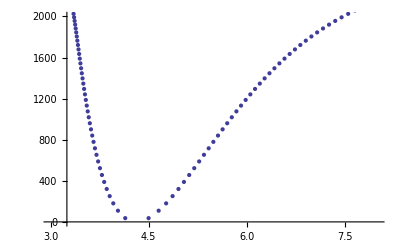

```mathematica
Y = Yc3SigmaPlusNa39K;
mu=muNa39K;
RKRPotc3SigmaPlusNa39K = Table[{v,e[v],a[v],b[v]},{v,0,50}];
Boundstatesc3SigmaPlusNa39K = Table[{v,e[v]},{v,0,50}];
RKRPotc3SigmaPlusNa39K//MatrixForm
Showc3SigmaPlusPot =Show[ListPlot[Table[{RKRPotc3SigmaPlusNa39K[[v,3]],RKRPotc3SigmaPlusNa39K[[v,2]]},{v,1,51}]],ListPlot[Table[{RKRPotc3SigmaPlusNa39K[[v,4]],RKRPotc3SigmaPlusNa39K[[v,2]]},{v,1,51}]], PlotRange->{{3,8},{0,2000}}]
```

### RKR From Ferber et al.:

```mathematica
RKRPotc3SigmaPlusNa39KFerber={{0,36.59,4.1422,4.4997},{1,109.02,4.0309,4.6535},{2,180.49,3.9596,4.7679},{3,250.98,3.9047,4.8666},{4,320.49,3.8593,4.9564},{5,389.02,3.8204,5.0405},{6,456.55,3.7862,5.1206},{7,523.08,3.7556,5.1978},{8,588.61,3.7279,5.2729},{9,653.13,3.7025,5.3464},{10,716.63,3.6792,5.4188},{11,779.11,3.6576,5.4903},{12,840.56,3.6375,5.5611},{13,900.98,3.6187,5.6317},{14,960.35,3.6011,5.702},{15,1018.69,3.5844,5.7723},{16,1075.97,3.5687,5.8427},{17,1132.19,3.5538,5.9133},{18,1187.35,3.5397,5.9843},{19,1241.44,3.5263,6.0558},{20,1294.45,3.5135,6.1278},{21,1346.38,3.5012,6.2006},{22,1397.23,3.4895,6.2741},{23,1446.98,3.4783,6.3485},{24,1495.63,3.4675,6.424},{25,1543.18,3.4571,6.5006},{26,1589.62,3.4471,6.5783},{27,1634.94,3.4374,6.6574},{28,1679.14,3.428,6.738},{29,1722.21,3.4188,6.8201},{30,1764.15,3.41,6.904},{31,1804.95,3.4013,6.9897},{32,1844.6,3.3928,7.0773},{33,1883.09,3.3845,7.1672},{34,1920.44,3.3763,7.2593},{35,1956.61,3.3683,7.354},{36,1991.62,3.3602,7.4514}};
```

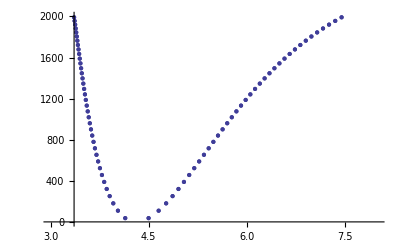

```mathematica
Show[ListPlot[Table[{RKRPotc3SigmaPlusNa39K[[v,3]],RKRPotc3SigmaPlusNa39K[[v,2]]},{v,1,37}]],ListPlot[Table[{RKRPotc3SigmaPlusNa39K[[v,4]],RKRPotc3SigmaPlusNa39K[[v,2]]},{v,1,37}]],
ListPlot[Table[{RKRPotc3SigmaPlusNa39KFerber[[v,3]],RKRPotc3SigmaPlusNa39KFerber[[v,2]]},{v,1,37}]],ListPlot[Table[{RKRPotc3SigmaPlusNa39KFerber[[v,4]],RKRPotc3SigmaPlusNa39KFerber[[v,2]]},{v,1,37}]], PlotRange->{{3,8},{0,2000}}]
```

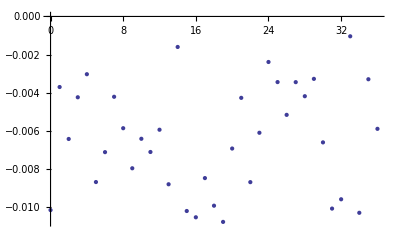

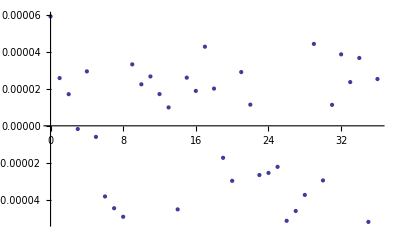

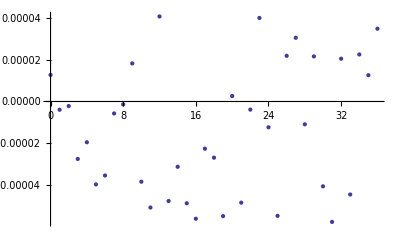

```mathematica
ListPlot[Table[{RKRPotc3SigmaPlusNa39K[[v,1]],RKRPotc3SigmaPlusNa39K[[v,2]]-RKRPotc3SigmaPlusNa39KFerber[[v,2]]},{v,1,37}]]
ListPlot[Table[{RKRPotc3SigmaPlusNa39K[[v,1]],RKRPotc3SigmaPlusNa39K[[v,3]]-RKRPotc3SigmaPlusNa39KFerber[[v,3]]},{v,1,37}]]
ListPlot[Table[{RKRPotc3SigmaPlusNa39K[[v,1]],RKRPotc3SigmaPlusNa39K[[v,4]]-RKRPotc3SigmaPlusNa39KFerber[[v,4]]},{v,1,37}]]
```

### Finding energies of Na^40 K and Na^41 K c3Σ+ via mass scaling of Dunham coefficients: Dunham, Phys. Rev. 41, 721 (1932) http://prola.aps.org/abstract/PR/v41/i6/p721_1

#### Correction terms to simple mass scaling (essentially negligible for us...)

```mathematica
Y = Yc3SigmaPlusNa39K;
bc = Y;
bc[[All,All]]=0;
a1 = Y[[1+1,1+1]] Y[[1+1,0+1]]/(6 Y[[0+1,1+1]]^2)-1;
bc[[0+1,1+1]] = Y[[1+1,0+1]]^2 Y[[2+1,1+1]]/(4 Y[[0+1,1+1]]^3)+16 a1 Y[[2+1,0+1]]/(3Y[[0+1,1+1]])-8a1 - 6 a1^2+4 a1^3;
bc[[1+1,0+1]] = 5Y[[1+1,0+1]] Y[[3+1,0+1]]/(4 Y[[0+1,1+1]]^2)+a1 Y[[1+1,0+1]]^2 Y[[2+1,1+1]]/(3 Y[[0+1,1+1]]^3)-10 a1 -20 a1^2-15 a1^3/2-5 a1^4/2+Y[[2+1,0+1]](4 a1 + 16 a1^2/3)/Y[[0+1,1+1]]+Y[[2+1,0+1]]^2/(2 Y[[0+1,1+1]]^2);
bc[[0+1,2+1]] = 73/2+37a1 + 67 a1^2/2+33 a1^3-6 a1^4-9Y[[1+1,0+1]] Y[[3+1,0+1]]/(2 Y[[0+1,1+1]]^2)+Y[[1+1,0+1]]^2 Y[[2+1,1+1]](3-11a1/6)/(2 Y[[0+1,1+1]]^3)-Y[[2+1,0+1]](130/3+4a1+74 a1^2/3)/(2Y[[0+1,1+1]])+31 Y[[2+1,0+1]]^2/(9 Y[[0+1,1+1]]^2);
typicalcorrection = bc[[0+1,1+1]](Yc3SigmaPlusNa39K[[0+1,1+1]]/Yc3SigmaPlusNa39K[[1+1,0+1]])^2(muNa39K-muNa40K)/muNa40K
```

7.50479×10^-8

#### Do mass scaling for Na40K

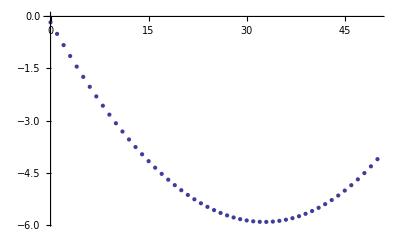

```mathematica
Yc3SigmaPlusNa40K = Yc3SigmaPlusNa39K;
For[i=1,i<10,i++,
For[j=0,j<3,j++,
Yc3SigmaPlusNa40K[[i+1,j+1]]=Yc3SigmaPlusNa39K[[i+1,j+1]](muNa39K/muNa40K)^((i+2j)/2)(1+bc[[i+1,j+1]](Yc3SigmaPlusNa39K[[0+1,1+1]]/Yc3SigmaPlusNa39K[[1+1,0+1]])^2(muNa39K-muNa40K)/muNa40K)
]]
Y=Yc3SigmaPlusNa40K;
mu = muNa40K;
Boundstatesc3SigmaPlusNa40K = Table[{v,e[v]},{v,0,50}];
PAlinesc3SigmaPlusNa40K =Table[{v,Tec3sigmaplus - DeX+Boundstatesc3SigmaPlusNa40K[[v+1,2]]},{v,0,50}];
PAwavelengthc3SigmaPlusNa40K = Table[{v,1/100/PAlinesc3SigmaPlusNa40K[[v+1,2]] 10^9},{v,0,50}];
Isotopeshiftc3SigmaPlusNa40K = Table[{v,Boundstatesc3SigmaPlusNa40K[[v+1,2]]-Boundstatesc3SigmaPlusNa39K[[v+1,2]]},{v,0,50}];
ListPlot[Isotopeshiftc3SigmaPlusNa40K]
```

#### Do mass scaling for Na41K

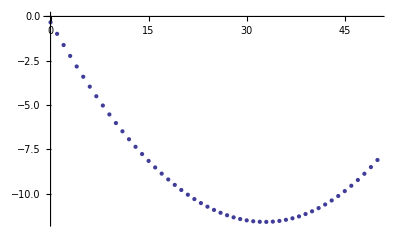

```mathematica
Yc3SigmaPlusNa41K = Yc3SigmaPlusNa39K;
For[i=1,i<10,i++,
For[j=0,j<3,j++,
Yc3SigmaPlusNa41K[[i+1,j+1]]=Yc3SigmaPlusNa39K[[i+1,j+1]](muNa39K/muNa41K)^((i+2j)/2)(1+bc[[i+1,j+1]](Yc3SigmaPlusNa39K[[0+1,1+1]]/Yc3SigmaPlusNa39K[[1+1,0+1]])^2(muNa39K-muNa41K)/muNa41K)
]]
Y=Yc3SigmaPlusNa41K;
mu = muNa41K;
Boundstatesc3SigmaPlusNa41K = Table[{v,e[v]},{v,0,50}];
PAlinesc3SigmaPlusNa41K =Table[{v,Tec3sigmaplus - DeX+Boundstatesc3SigmaPlusNa41K[[v+1,2]]},{v,0,50}];
PAwavelengthc3SigmaPlusNa41K = Table[{v,1/100/PAlinesc3SigmaPlusNa41K[[v+1,2]] 10^9},{v,0,50}];
Isotopeshiftc3SigmaPlusNa41K = Table[{v,Boundstatesc3SigmaPlusNa41K[[v+1,2]]-Boundstatesc3SigmaPlusNa39K[[v+1,2]]},{v,0,50}];
ListPlot[Isotopeshiftc3SigmaPlusNa41K]
```

## b3Π

### b3Π state for Na^39 K R. Ferber et al., J. Chem. Phys. 112, 5740 (2000) http://dx.doi.org/10.1063/1.481149

```mathematica
mu = muNa39K;
Teb3Pi= 11562.18;
vmaxb3Pi = 75;
Y=Table[0,{i,1,10},{j,1,3}];
Y[[All,All]]=0;
Y[[0+1,0+1]]=0;
Y[[1+1,0+1]]=120.371380;
Y[[2+1,0+1]]=-0.332024;
Y[[3+1,0+1]]=-0.104098 10^-2;
Y[[4+1,0+1]]=0.386127 10^-4;
Y[[5+1,0+1]]=-0.123100 10^-5;
Y[[6+1,0+1]]=0.143700 10^-7;
Y[[7+1,0+1]]=-0.805024 10^-10;
Y[[0+1,1+1]]=0.950673 10^-1;
Y[[1+1,1+1]]=-0.328708 10^-3;
Y[[2+1,1+1]]=-0.205156 10^-5;
Y[[3+1,1+1]]=0.361430 10^-7;
Y[[4+1,1+1]]=-0.186723 10^-8;
Y[[5+1,1+1]]=0.278352 10^-10;
Y[[6+1,1+1]]=-0.235550 10^-12;
Y[[0+1,2+1]]=-0.230157 10^-6;
Y[[1+1,2+1]]=-0.178322 10^-8;
Y[[2+1,2+1]]=0.802326 10^-10;
Y[[3+1,2+1]]=-0.159840 10^-11;
Yb3PiNa39K = Y;
Y//MatrixForm
```

(0 | 0.0950673 | -2.30157×10^-7
120.371 | -0.000328708 | -1.78322×10^-9
-0.332024 | -2.05156×10^-6 | 8.02326×10^-11
-0.00104098 | 3.6143×10^-8 | -1.5984×10^-12
0.0000386127 | -1.86723×10^-9 | 0
-1.231×10^-6 | 2.78352×10^-11 | 0
1.437×10^-8 | -2.3555×10^-13 | 0
-8.05024×10^-11 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

### RKR Potential for b3Π:

CompiledFunction::cfsa: Argument 0.5  + v
 at position 1 should be a "machine-size real number".

General::stop: Further output of CompiledFunction :: cfsa will be suppressed during this calculation.

(0 | 60.1026 | 3.36747 | 3.64615
1 | 179.807 | 3.27455 | 3.75838
2 | 298.838 | 3.21316 | 3.83925
3 | 417.193 | 3.16474 | 3.90731
4 | 534.867 | 3.12392 | 3.96794
5 | 651.855 | 3.08824 | 4.02361
6 | 768.156 | 3.05633 | 4.07568
7 | 883.765 | 3.02734 | 4.125
8 | 998.681 | 3.00069 | 4.17216
9 | 1112.9 | 2.97598 | 4.21757
10 | 1226.42 | 2.9529 | 4.26152
11 | 1339.24 | 2.93123 | 4.30426
12 | 1451.35 | 2.91078 | 4.34597
13 | 1562.75 | 2.8914 | 4.3868
14 | 1673.44 | 2.87299 | 4.42687
15 | 1783.42 | 2.85543 | 4.46629
16 | 1892.68 | 2.83866 | 4.50515
17 | 2001.21 | 2.82259 | 4.54351
18 | 2109.02 | 2.80718 | 4.58145
19 | 2216.09 | 2.79236 | 4.61903
20 | 2322.42 | 2.7781 | 4.65631
21 | 2428. | 2.76435 | 4.69332
22 | 2532.84 | 2.75108 | 4.73011
23 | 2636.91 | 2.73826 | 4.76673
24 | 2740.22 | 2.72586 | 4.80321
25 | 2842.75 | 2.71386 | 4.83959
26 | 2944.5 | 2.70223 | 4.8759
27 | 3045.45 | 2.69096 | 4.91218
28 | 3145.6 | 2.68002 | 4.94846
29 | 3244.93 | 2.66941 | 4.98476
30 | 3343.44 | 2.6591 | 5.02113
31 | 3441.11 | 2.64909 | 5.05758
32 | 3537.93 | 2.63936 | 5.09415
33 | 3633.88 | 2.62989 | 5.13087
34 | 3728.96 | 2.62068 | 5.16777
35 | 3823.14 | 2.61172 | 5.20489
36 | 3916.41 | 2.60301 | 5.24225
37 | 4008.76 | 2.59452 | 5.27988
38 | 4100.16 | 2.58626 | 5.31783
39 | 4190.6 | 2.57822 | 5.35612
40 | 4280.06 | 2.57039 | 5.39479
41 | 4368.52 | 2.56277 | 5.43389
42 | 4455.96 | 2.55535 | 5.47345
43 | 4542.35 | 2.54813 | 5.51352
44 | 4627.68 | 2.5411 | 5.55414
45 | 4711.91 | 2.53427 | 5.59537
46 | 4795.02 | 2.52762 | 5.63726
47 | 4876.98 | 2.52115 | 5.67987
48 | 4957.76 | 2.51487 | 5.72326
49 | 5037.34 | 2.50876 | 5.76749
50 | 5115.68 | 2.50283 | 5.81265
51 | 5192.74 | 2.49708 | 5.85882
52 | 5268.49 | 2.4915 | 5.90608
53 | 5342.89 | 2.48609 | 5.95454
54 | 5415.89 | 2.48085 | 6.00431
55 | 5487.46 | 2.47579 | 6.05551
56 | 5557.55 | 2.47089 | 6.10828
57 | 5626.1 | 2.46616 | 6.16277
58 | 5693.07 | 2.46159 | 6.21915
59 | 5758.4 | 2.45719 | 6.27763
60 | 5822.03 | 2.45294 | 6.33842
61 | 5883.9 | 2.44886 | 6.40178
62 | 5943.93 | 2.44492 | 6.46801
63 | 6002.06 | 2.44113 | 6.53745
64 | 6058.22 | 2.43748 | 6.61049
65 | 6112.32 | 2.43396 | 6.68761
66 | 6164.27 | 2.43054 | 6.76935
67 | 6213.98 | 2.42722 | 6.85639
68 | 6261.36 | 2.42397 | 6.94953
69 | 6306.3 | 2.42075 | 7.04977
70 | 6348.68 | 2.41752 | 7.15834
71 | 6388.41 | 2.41422 | 7.27682
72 | 6425.33 | 2.41074 | 7.40725
73 | 6459.33 | 2.40699 | 7.55235
74 | 6490.27 | 2.40276 | 7.71585
75 | 6517.98 | 2.3978 | 7.90307)

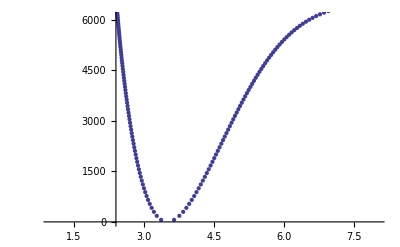

```mathematica
Y=Yb3PiNa39K;
mu = muNa39K;
RKRPotb3PiNa39K = Table[{v,e[v],a[v],b[v]},{v,0,vmaxb3Pi}];
Boundstatesb3PiNa39K = Table[{v,e[v]},{v,0,vmaxb3Pi}];
RKRPotb3PiNa39K//MatrixForm
Showb3PiPot=Show[ListPlot[Table[{RKRPotb3PiNa39K[[v,3]],RKRPotb3PiNa39K[[v,2]]},{v,1,vmaxb3Pi+1}]],ListPlot[Table[{RKRPotb3PiNa39K[[v,4]],RKRPotb3PiNa39K[[v,2]]},{v,1,vmaxb3Pi+1}]], PlotRange->{{1,8},{0,6100}}]
```

### Finding energies of Na^40 K and Na^41 K b3Π via mass scaling of Dunham coefficients: Dunham, Phys. Rev. 41, 721 (1932) http://prola.aps.org/abstract/PR/v41/i6/p721_1

#### Correction terms to simple mass scaling (essentially negligible for us...)

```mathematica
Y = Yb3PiNa39K;
bc = Y;
bc[[All,All]]=0;
a1 = Y[[1+1,1+1]] Y[[1+1,0+1]]/(6 Y[[0+1,1+1]]^2)-1;
bc[[0+1,1+1]] = Y[[1+1,0+1]]^2 Y[[2+1,1+1]]/(4 Y[[0+1,1+1]]^3)+16 a1 Y[[2+1,0+1]]/(3Y[[0+1,1+1]])-8a1 - 6 a1^2+4 a1^3;
bc[[1+1,0+1]] = 5Y[[1+1,0+1]] Y[[3+1,0+1]]/(4 Y[[0+1,1+1]]^2)+a1 Y[[1+1,0+1]]^2 Y[[2+1,1+1]]/(3 Y[[0+1,1+1]]^3)-10 a1 -20 a1^2-15 a1^3/2-5 a1^4/2+Y[[2+1,0+1]](4 a1 + 16 a1^2/3)/Y[[0+1,1+1]]+Y[[2+1,0+1]]^2/(2 Y[[0+1,1+1]]^2);
bc[[0+1,2+1]] = 73/2+37a1 + 67 a1^2/2+33 a1^3-6 a1^4-9Y[[1+1,0+1]] Y[[3+1,0+1]]/(2 Y[[0+1,1+1]]^2)+Y[[1+1,0+1]]^2 Y[[2+1,1+1]](3-11a1/6)/(2 Y[[0+1,1+1]]^3)-Y[[2+1,0+1]](130/3+4a1+74 a1^2/3)/(2Y[[0+1,1+1]])+31 Y[[2+1,0+1]]^2/(9 Y[[0+1,1+1]]^2);
typicalcorrection = bc[[0+1,1+1]](Yb3PiNa39K[[0+1,1+1]]/Yb3PiNa39K[[1+1,0+1]])^2(muNa39K-muNa40K)/muNa40K
```

7.20121×10^-9

#### Do mass scaling for Na40K

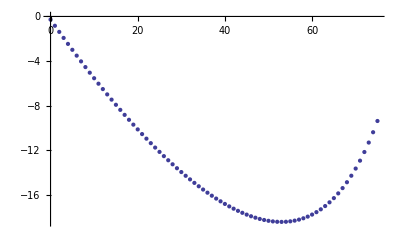

```mathematica
Yb3PiNa40K = Yb3PiNa39K;
For[i=1,i<10,i++,
For[j=0,j<3,j++,
Yb3PiNa40K[[i+1,j+1]]=Yb3PiNa39K[[i+1,j+1]](muNa39K/muNa40K)^((i+2j)/2)(1+bc[[i+1,j+1]](Yb3PiNa39K[[0+1,1+1]]/Yb3PiNa39K[[1+1,0+1]])^2(muNa39K-muNa40K)/muNa40K)
]]
Y=Yb3PiNa40K;
mu = muNa40K;
Boundstatesb3PiNa40K = Table[{v,e[v]},{v,0,vmaxb3Pi}];
PAlinesb3PiNa40K =Table[{v,Teb3Pi - DeX+Boundstatesb3PiNa40K[[v+1,2]]},{v,0,vmaxb3Pi}];
PAwavelengthb3PiNa40K = Table[{v,1/100/PAlinesb3PiNa40K[[v+1,2]] 10^9},{v,0,vmaxb3Pi}];
Isotopeshiftb3PiNa40K = Table[{v,Boundstatesb3PiNa40K[[v+1,2]]-Boundstatesb3PiNa39K[[v+1,2]]},{v,0,vmaxb3Pi}];
ListPlot[Isotopeshiftb3PiNa40K]
```

#### Do mass scaling for Na41K

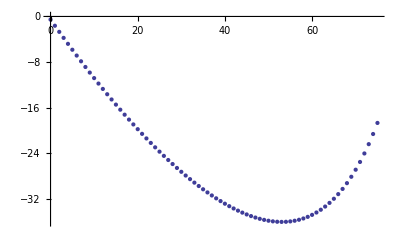

```mathematica
Yb3PiNa41K = Yb3PiNa39K;
For[i=1,i<10,i++,
For[j=0,j<3,j++,
Yb3PiNa41K[[i+1,j+1]]=Yb3PiNa39K[[i+1,j+1]](muNa39K/muNa41K)^((i+2j)/2)(1+bc[[i+1,j+1]](Yb3PiNa39K[[0+1,1+1]]/Yb3PiNa39K[[1+1,0+1]])^2(muNa39K-muNa41K)/muNa41K)
]]
Y=Yb3PiNa41K;
mu = muNa41K;
Boundstatesb3PiNa41K = Table[{v,e[v]},{v,0,vmaxb3Pi}];
PAlinesb3PiNa41K =Table[{v,Teb3Pi - DeX+Boundstatesb3PiNa41K[[v+1,2]]},{v,0,vmaxb3Pi}];
PAwavelengthb3PiNa41K = Table[{v,1/100/PAlinesb3PiNa41K[[v+1,2]] 10^9},{v,0,vmaxb3Pi}];
Isotopeshiftb3PiNa41K = Table[{v,Boundstatesb3PiNa41K[[v+1,2]]-Boundstatesb3PiNa39K[[v+1,2]]},{v,0,vmaxb3Pi}];
ListPlot[Isotopeshiftb3PiNa41K]
```

## A1Σ+

### A1Σ+ state for Na^39 K Ross, Clements, Barrow, J. Mol. Spec. 127, 546 (1988)

```mathematica
mu = muNa39K;
TeA1SigmaPlus= 12137.272;
vmaxA1SigmaPlus = 100;
Y=Table[0,{i,1,10},{j,1,3}];
Y[[All,All]]=0;
Y[[0+1,0+1]]=0;
Y[[1+1,0+1]]=81.250506;
Y[[2+1,0+1]]=-0.27470815;
Y[[3+1,0+1]]=0.41931994 10^-2;
Y[[4+1,0+1]]=-0.7720508 10^-4;
Y[[5+1,0+1]]=0.6932446 10^-6;
Y[[6+1,0+1]]=-0.282698 10^-8;
Y[[0+1,1+1]]=0.0661371;
Y[[1+1,1+1]]=-0.360162 10^-3;
Y[[2+1,1+1]]=0.3300504 10^-5;
Y[[3+1,1+1]]=-0.3409183 10^-7;
Y[[0+1,2+1]]=0.16600 10^-6;
Y[[1+1,2+1]]=-0.6343 10^-9;
YA1SigmaPlusNa39K = Y;
Y//MatrixForm
```

(0 | 0.0661371 | 1.66×10^-7
81.2505 | -0.000360162 | -6.343×10^-10
-0.274708 | 3.3005×10^-6 | 0
0.0041932 | -3.40918×10^-8 | 0
-0.0000772051 | 0 | 0
6.93245×10^-7 | 0 | 0
-2.82698×10^-9 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

### RKR Potential for A1Σ+:

CompiledFunction::cfsa: Argument 0.5  + v
 at position 1 should be a "machine-size real number".

General::stop: Further output of CompiledFunction :: cfsa will be suppressed during this calculation.

(0 | 40.5571 | 4.03624 | 4.37553
1 | 121.271 | 3.92568 | 4.51495
2 | 201.472 | 3.85334 | 4.6161
3 | 281.18 | 3.79669 | 4.7015
4 | 360.416 | 3.74918 | 4.77768
5 | 439.198 | 3.70785 | 4.84763
6 | 517.543 | 3.67103 | 4.913
7 | 595.467 | 3.63769 | 4.97482
8 | 672.983 | 3.60715 | 5.03379
9 | 750.105 | 3.5789 | 5.09039
10 | 826.844 | 3.55258 | 5.145
11 | 903.211 | 3.52792 | 5.1979
12 | 979.214 | 3.50469 | 5.24931
13 | 1054.86 | 3.48272 | 5.2994
14 | 1130.16 | 3.46186 | 5.34833
15 | 1205.12 | 3.442 | 5.39622
16 | 1279.75 | 3.42303 | 5.44317
17 | 1354.04 | 3.40487 | 5.48928
18 | 1428.01 | 3.38746 | 5.53461
19 | 1501.66 | 3.37071 | 5.57925
20 | 1574.98 | 3.35459 | 5.62325
21 | 1647.98 | 3.33904 | 5.66666
22 | 1720.67 | 3.32402 | 5.70954
23 | 1793.04 | 3.3095 | 5.75192
24 | 1865.1 | 3.29543 | 5.79386
25 | 1936.84 | 3.28179 | 5.83539
26 | 2008.27 | 3.26856 | 5.87654
27 | 2079.37 | 3.2557 | 5.91735
28 | 2150.16 | 3.2432 | 5.95785
29 | 2220.63 | 3.23103 | 5.99806
30 | 2290.78 | 3.21919 | 6.03802
31 | 2360.6 | 3.20764 | 6.07774
32 | 2430.1 | 3.19639 | 6.11725
33 | 2499.26 | 3.18541 | 6.15659
34 | 2568.1 | 3.17469 | 6.19576
35 | 2636.6 | 3.16422 | 6.23478
36 | 2704.76 | 3.15399 | 6.27369
37 | 2772.58 | 3.14399 | 6.3125
38 | 2840.06 | 3.13422 | 6.35123
39 | 2907.18 | 3.12466 | 6.3899
40 | 2973.96 | 3.11531 | 6.42853
41 | 3040.37 | 3.10616 | 6.46713
42 | 3106.43 | 3.0972 | 6.50572
43 | 3172.12 | 3.08844 | 6.54432
44 | 3237.43 | 3.07986 | 6.58296
45 | 3302.38 | 3.07146 | 6.62163
46 | 3366.94 | 3.06323 | 6.66038
47 | 3431.12 | 3.05518 | 6.6992
48 | 3494.9 | 3.0473 | 6.73812
49 | 3558.3 | 3.03958 | 6.77716
50 | 3621.28 | 3.03202 | 6.81634
51 | 3683.87 | 3.02463 | 6.85566
52 | 3746.03 | 3.01739 | 6.89516
53 | 3807.78 | 3.0103 | 6.93486
54 | 3869.1 | 3.00336 | 6.97476
55 | 3929.99 | 2.99658 | 7.0149
56 | 3990.44 | 2.98994 | 7.0553
57 | 4050.43 | 2.98344 | 7.09597
58 | 4109.97 | 2.97709 | 7.13694
59 | 4169.05 | 2.97088 | 7.17824
60 | 4227.65 | 2.9648 | 7.2199
61 | 4285.76 | 2.95886 | 7.26193
62 | 4343.38 | 2.95305 | 7.30437
63 | 4400.5 | 2.94738 | 7.34726
64 | 4457.09 | 2.94183 | 7.39062
65 | 4513.17 | 2.9364 | 7.43449
66 | 4568.69 | 2.9311 | 7.47891
67 | 4623.67 | 2.92591 | 7.52392
68 | 4678.08 | 2.92084 | 7.56956
69 | 4731.9 | 2.91587 | 7.61588
70 | 4785.12 | 2.91101 | 7.66293
71 | 4837.72 | 2.90625 | 7.71078
72 | 4889.69 | 2.90158 | 7.75946
73 | 4941.01 | 2.897 | 7.80906
74 | 4991.64 | 2.8925 | 7.85965
75 | 5041.59 | 2.88807 | 7.9113
76 | 5090.81 | 2.88371 | 7.96409
77 | 5139.29 | 2.8794 | 8.01812
78 | 5187. | 2.87513 | 8.07349
79 | 5233.91 | 2.8709 | 8.13033
80 | 5279.99 | 2.86668 | 8.18874
81 | 5325.22 | 2.86246 | 8.24887
82 | 5369.56 | 2.85823 | 8.31088
83 | 5412.98 | 2.85397 | 8.37494
84 | 5455.43 | 2.84966 | 8.44124
85 | 5496.89 | 2.84526 | 8.51001
86 | 5537.32 | 2.84077 | 8.58149
87 | 5576.66 | 2.83613 | 8.65597
88 | 5614.88 | 2.83132 | 8.73378
89 | 5651.92 | 2.8263 | 8.81528
90 | 5687.75 | 2.82102 | 8.90092
91 | 5722.3 | 2.81541 | 8.99119
92 | 5755.53 | 2.80943 | 9.08672
93 | 5787.37 | 2.80298 | 9.1882
94 | 5817.77 | 2.79598 | 9.29651
95 | 5846.65 | 2.78831 | 9.41269
96 | 5873.97 | 2.77983 | 9.53805
97 | 5899.64 | 2.77037 | 9.67421
98 | 5923.59 | 2.75971 | 9.82327
99 | 5945.74 | 2.74756 | 9.98798
100 | 5966.03 | 2.73354 | 10.172)

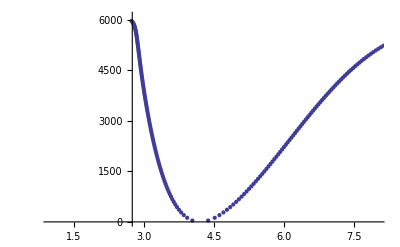

```mathematica
mu = muNa39K;
Y=YA1SigmaPlusNa39K;
RKRPotA1SigmaPlusNa39K = Table[{v,e[v],a[v],b[v]},{v,0,vmaxA1SigmaPlus}];
BoundstatesA1SigmaPlusNa39K = Table[{v,e[v]},{v,0,vmaxA1SigmaPlus}];
RKRPotA1SigmaPlusNa39K//MatrixForm
ShowA1SigmaPlusPot=Show[ListPlot[Table[{RKRPotA1SigmaPlusNa39K[[v,3]],RKRPotA1SigmaPlusNa39K[[v,2]]},{v,1,vmaxA1SigmaPlus+1}]],ListPlot[Table[{RKRPotA1SigmaPlusNa39K[[v,4]],RKRPotA1SigmaPlusNa39K[[v,2]]},{v,1,vmaxA1SigmaPlus+1}]], PlotRange->{{1,8},{0,6100}}]
```

### Finding energies of Na^40 K and Na^41 K A1Σ+ via mass scaling of Dunham coefficients: Dunham, Phys. Rev. 41, 721 (1932) http://prola.aps.org/abstract/PR/v41/i6/p721_1

#### Correction terms to simple mass scaling (essentially negligible for us...)

```mathematica
Y = YA1SigmaPlusNa39K;
bc = Y;
bc[[All,All]]=0;
a1 = Y[[1+1,1+1]] Y[[1+1,0+1]]/(6 Y[[0+1,1+1]]^2)-1;
bc[[0+1,1+1]] = Y[[1+1,0+1]]^2 Y[[2+1,1+1]]/(4 Y[[0+1,1+1]]^3)+16 a1 Y[[2+1,0+1]]/(3Y[[0+1,1+1]])-8a1 - 6 a1^2+4 a1^3;
bc[[1+1,0+1]] = 5Y[[1+1,0+1]] Y[[3+1,0+1]]/(4 Y[[0+1,1+1]]^2)+a1 Y[[1+1,0+1]]^2 Y[[2+1,1+1]]/(3 Y[[0+1,1+1]]^3)-10 a1 -20 a1^2-15 a1^3/2-5 a1^4/2+Y[[2+1,0+1]](4 a1 + 16 a1^2/3)/Y[[0+1,1+1]]+Y[[2+1,0+1]]^2/(2 Y[[0+1,1+1]]^2);
bc[[0+1,2+1]] = 73/2+37a1 + 67 a1^2/2+33 a1^3-6 a1^4-9Y[[1+1,0+1]] Y[[3+1,0+1]]/(2 Y[[0+1,1+1]]^2)+Y[[1+1,0+1]]^2 Y[[2+1,1+1]](3-11a1/6)/(2 Y[[0+1,1+1]]^3)-Y[[2+1,0+1]](130/3+4a1+74 a1^2/3)/(2Y[[0+1,1+1]])+31 Y[[2+1,0+1]]^2/(9 Y[[0+1,1+1]]^2);
typicalcorrection = bc[[0+1,1+1]](YA1SigmaPlusNa39K[[0+1,1+1]]/YA1SigmaPlusNa39K[[1+1,0+1]])^2(muNa39K-muNa40K)/muNa40K
```

-1.10272×10^-7

#### Do mass scaling for Na40K

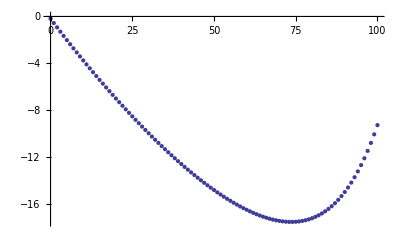

```mathematica
YA1SigmaPlusNa40K = YA1SigmaPlusNa39K;
For[i=1,i<10,i++,
For[j=0,j<3,j++,
YA1SigmaPlusNa40K[[i+1,j+1]]=YA1SigmaPlusNa39K[[i+1,j+1]](muNa39K/muNa40K)^((i+2j)/2)(1+bc[[i+1,j+1]](YA1SigmaPlusNa39K[[0+1,1+1]]/YA1SigmaPlusNa39K[[1+1,0+1]])^2(muNa39K-muNa40K)/muNa40K)
]]
Y=YA1SigmaPlusNa40K;
mu = muNa40K;
BoundstatesA1SigmaPlusNa40K = Table[{v,e[v]},{v,0,vmaxA1SigmaPlus}];
PAlinesA1SigmaPlusNa40K =Table[{v,TeA1SigmaPlus - DeX+BoundstatesA1SigmaPlusNa40K[[v+1,2]]},{v,0,vmaxA1SigmaPlus}];
PAwavelengthA1SigmaPlusNa40K = Table[{v,1/100/PAlinesA1SigmaPlusNa40K[[v+1,2]] 10^9},{v,0,vmaxA1SigmaPlus}];
IsotopeshiftA1SigmaPlusNa40K = Table[{v,BoundstatesA1SigmaPlusNa40K[[v+1,2]]-BoundstatesA1SigmaPlusNa39K[[v+1,2]]},{v,0,vmaxA1SigmaPlus}];
ListPlot[IsotopeshiftA1SigmaPlusNa40K]
```

#### Do mass scaling for Na41K

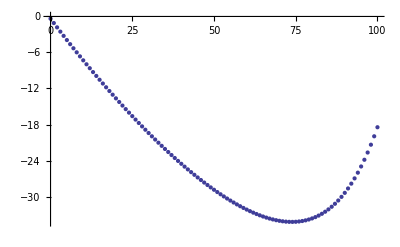

```mathematica
YA1SigmaPlusNa41K = YA1SigmaPlusNa39K;
For[i=1,i<10,i++,
For[j=0,j<3,j++,
YA1SigmaPlusNa41K[[i+1,j+1]]=YA1SigmaPlusNa39K[[i+1,j+1]](muNa39K/muNa41K)^((i+2j)/2)(1+bc[[i+1,j+1]](YA1SigmaPlusNa39K[[0+1,1+1]]/YA1SigmaPlusNa39K[[1+1,0+1]])^2(muNa39K-muNa41K)/muNa41K)
]]
Y=YA1SigmaPlusNa41K;
mu = muNa41K;
BoundstatesA1SigmaPlusNa41K = Table[{v,e[v]},{v,0,vmaxA1SigmaPlus}];
PAlinesA1SigmaPlusNa41K =Table[{v,TeA1SigmaPlus - DeX+BoundstatesA1SigmaPlusNa41K[[v+1,2]]},{v,0,vmaxA1SigmaPlus}];
PAwavelengthA1SigmaPlusNa41K = Table[{v,1/100/PAlinesA1SigmaPlusNa41K[[v+1,2]] 10^9},{v,0,vmaxA1SigmaPlus}];
IsotopeshiftA1SigmaPlusNa41K = Table[{v,BoundstatesA1SigmaPlusNa41K[[v+1,2]]-BoundstatesA1SigmaPlusNa39K[[v+1,2]]},{v,0,vmaxA1SigmaPlus}];
ListPlot[IsotopeshiftA1SigmaPlusNa41K]
```

## Summary

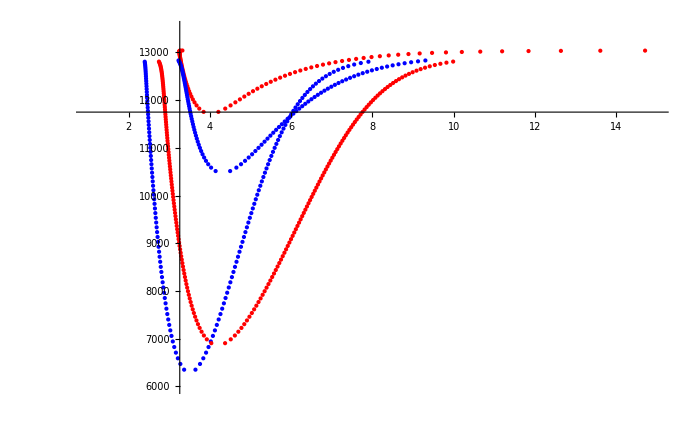

```mathematica
Show[ListPlot[Table[{RKRPotB1PiNa39K[[v,3]],RKRPotB1PiNa39K[[v,2]]+TeB1Pi-DeX},{v,1,44}],PlotStyle->{Red}],ListPlot[Table[{RKRPotB1PiNa39K[[v,4]],RKRPotB1PiNa39K[[v,2]]+TeB1Pi-DeX},{v,1,44}],PlotStyle->{Red}],
ListPlot[Table[{RKRPotc3SigmaPlusNa39K[[v,3]],RKRPotc3SigmaPlusNa39K[[v,2]]+Tec3sigmaplus-DeX},{v,1,vmaxc3SigmaPlus+1}],PlotStyle->{Blue}],
ListPlot[Table[{RKRPotc3SigmaPlusNa39K[[v,4]],RKRPotc3SigmaPlusNa39K[[v,2]]+Tec3sigmaplus-DeX},{v,1,vmaxc3SigmaPlus+1}],PlotStyle->{Blue}],
ListPlot[Table[{RKRPotb3PiNa39K[[v,3]],RKRPotb3PiNa39K[[v,2]]+Teb3Pi-DeX},{v,1,vmaxb3Pi+1}],PlotStyle->{Blue}],
ListPlot[Table[{RKRPotb3PiNa39K[[v,4]],RKRPotb3PiNa39K[[v,2]]+Teb3Pi-DeX},{v,1,vmaxb3Pi+1}],PlotStyle->{Blue}],
ListPlot[Table[{RKRPotA1SigmaPlusNa39K[[v,3]],RKRPotA1SigmaPlusNa39K[[v,2]]+TeA1SigmaPlus-DeX},{v,1,vmaxA1SigmaPlus}],PlotStyle->{Red}],
ListPlot[Table[{RKRPotA1SigmaPlusNa39K[[v,4]],RKRPotA1SigmaPlusNa39K[[v,2]]+TeA1SigmaPlus-DeX},{v,1,vmaxA1SigmaPlus}],PlotStyle->{Red}],PlotRange->{{1,15},{6000,13500}}]
```

```mathematica
FoundLines=-{772.366,772.951,774.362,775.191,777.017,778.045,779.824,781.522,782.881,784.25,785.66,785.75,787.27,788.87,790.58,790.97,792.311,794.17,796.151,800.194,800.209,800.22,800.231,802.381,802.394,804.556,804.574,804.603,810.966,813.701,817.59,819.705,829.121,832.42};
FoundLines=-{772.366,772.951,774.362,775.191,777.017,778.045,779.824,781.522,782.881,784.25,785.66,785.75,787.27,788.87,790.58,790.97,792.311,794.17,796.11,796.151,800.194,800.209,800.22,800.231,802.381,802.394,804.556,804.574,804.603,810.966,813.701,817.59,819.705,820.1,820.11,820.155,820.165,829.121,829.22,832.42,835.819,839.091};
WavenumberFoundLines=-1/FoundLines/10^-9/100;
WavenumberFoundLinesAbs=-1/FoundLines/10^-9/100+DeX;
Wavelengthgrid=Plot[-760,{x,0,2},PlotRange->{-760,-850},Frame->True];
GraphicsFoundLines=Graphics[Table[Line[{{0,FoundLines[[i]]},{5,FoundLines[[i]]}}],{i,1,Dimensions[FoundLines][[1]]}]];
GraphicsPAc3SigmaPlusNa40K =Graphics[Table[{Directive[Thick,Blue],Line[{{1.8,-PAwavelengthc3SigmaPlusNa40K[[i,2]]},{2.2,-PAwavelengthc3SigmaPlusNa40K[[i,2]]}}]},{i,1,Dimensions[PAwavelengthc3SigmaPlusNa40K][[1]]}]];
GraphicsPAB1PiNa40K = Graphics[Table[{Directive[Thick,Red],Line[{{0.8,-PAwavelengthB1PiNa40K[[i,2]]},{1.2,-PAwavelengthB1PiNa40K[[i,2]]}}]},{i,1,Dimensions[PAwavelengthB1PiNa40K][[1]]}]];
GraphicsPAb3PiNa40K = Graphics[Table[{Directive[Thick,Blue],Line[{{2.8,-PAwavelengthb3PiNa40K[[i,2]]},{3.2,-PAwavelengthb3PiNa40K[[i,2]]}}]},{i,1,Dimensions[PAwavelengthb3PiNa40K][[1]]}]];
GraphicsPAA1SigmaPlusNa40K = Graphics[Table[{Directive[Thick,Red],Line[{{3.8,-PAwavelengthA1SigmaPlusNa40K[[i,2]]},{4.2,-PAwavelengthA1SigmaPlusNa40K[[i,2]]}}]},{i,1,Dimensions[PAwavelengthA1SigmaPlusNa40K][[1]]}]];
```

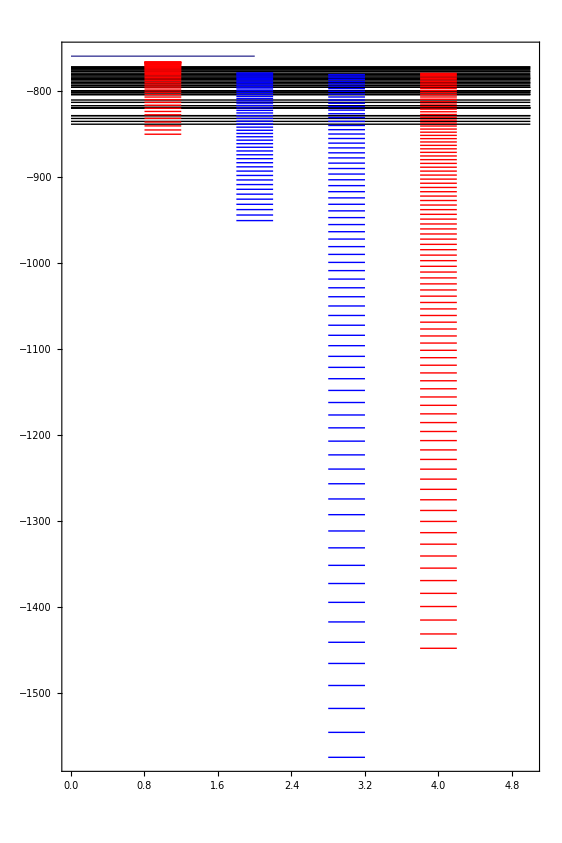

```mathematica
Show[Wavelengthgrid,GraphicsFoundLines,GraphicsPAc3SigmaPlusNa40K,GraphicsPAB1PiNa40K,GraphicsPAb3PiNa40K,GraphicsPAA1SigmaPlusNa40K,PlotRange->{{0.5,4.5},{-770,-850}},AspectRatio->1.5,BaseStyle->{FontWeight->"Bold",FontSize->24}]
```

```mathematica
PAwavelengthc3SigmaPlusNa40K[[26]]
PAwavelengthB1PiNa40K[[5]]
PAlinesc3SigmaPlusNa40K[[26]]
PAlinesB1PiNa40K[[5]]
```

{25,832.32}

{4,832.255}

{25,12014.6}

{4,12015.5}

```mathematica
1/100/(PAlinesc3SigmaPlusNa40K[[26,2]]+5211.75)*10^9
1/100/(PAlinesB1PiNa40K[[5,2]]+5211.75)*10^9
```

580.506

580.474

```mathematica
TableForm[Table[{v,PAlinesB1PiNa40K[[v+1,2]],PAwavelengthB1PiNa40K[[v+1,2]]},{v,0,vmaxB1Pi}]];
TableForm[Table[{v,PAlinesc3SigmaPlusNa40K[[v+1,2]],PAwavelengthc3SigmaPlusNa40K[[v+1,2]]},{v,0,vmaxc3SigmaPlus}]];
TableForm[Table[{v,PAlinesb3PiNa40K[[v+1,2]],PAwavelengthb3PiNa40K[[v+1,2]]},{v,0,vmaxb3Pi}]];
TableForm[Table[{v,PAlinesA1SigmaPlusNa40K[[v+1,2]],PAwavelengthA1SigmaPlusNa40K[[v+1,2]]},{v,0,vmaxA1SigmaPlus}]];
```

## Spin-Orbit coupling

### Find Perturbing levels found in Kowalczyk, J. Chem. Phys. 91, 2779 (1989)

#### Levels B1Pi v=1 and c3Σ+ v=21 do not cross but lie close enough to borrow intensity for the forbidden transitions:

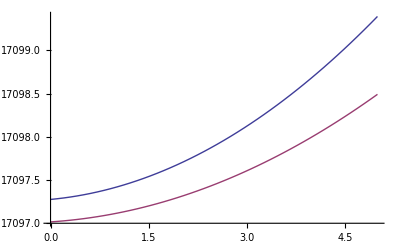

```mathematica
Plot[{TeB1Pi+Term[YB1PiNa39K,1,J],Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,21,J]},{J,0,5}]
```

#### Levels B1Pi v=13 and c3Σ+ v=36 do not cross but lie close enough to borrow intensity for the forbidden transitions: (If this is true, 3 wavenumbers difference is enough to borrow intensity!)

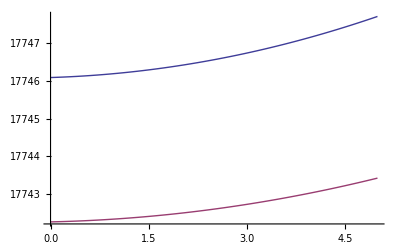

```mathematica
Plot[{TeB1Pi+Term[YB1PiNa39K,13,J],Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,36,J]},{J,0,5}]
```

#### Perturbation of B1Pi v=4 and c3Σ+ v=25, centered around J=13

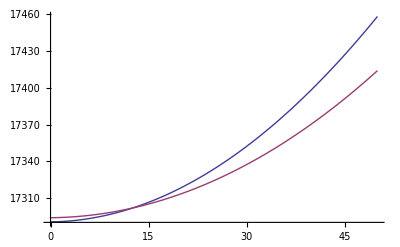

```mathematica
Plot[{TeB1Pi+Term[YB1PiNa39K,4,J],Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,25,J]},{J,0,50}]
```

#### Perturbation of B1Pi v=6 and c3Σ+ v=28, centered around J=33

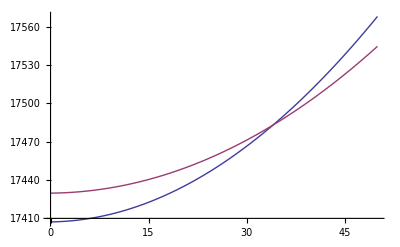

```mathematica
Plot[{TeB1Pi+Term[YB1PiNa39K,6,J],Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,28,J]},{J,0,50}]
```

#### Perturbation of B1Pi v=8 and c3Σ+ v=30, centered around J=5 (*Really?*) and b3Pi v=??? at J=23 (YES!!!)

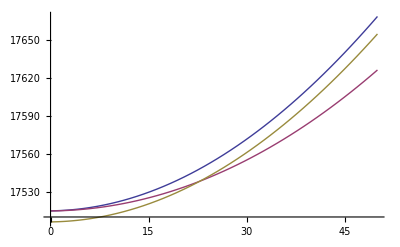

```mathematica
Plot[{TeB1Pi+Term[YB1PiNa39K,8,J],Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,30,J],Teb3Pi+Term[Yb3PiNa39K,62,J]},{J,0,50}]
```

#### Perturbation of B1Pi v=12 and c3Σ+ v=35, centered around J=14

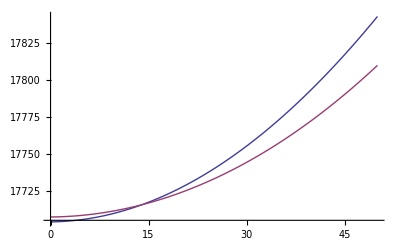

```mathematica
Plot[{TeB1Pi+Term[YB1PiNa39K,12,J],Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,35,J]},{J,0,50}]
```

### Find Perturbing levels found in Kowalczyk, J. of Mol. Spec. 151, 303 (1992)

#### Perturbation of B1Pi v=6 and c3Σ+ v=28, centered around J=33

```mathematica
Plot[{TeB1Pi+Term[YB1PiNa39K,6,J],Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,28,J]},{J,0,50}]
```

-Graphics-

#### Perturbation of B1Pi v=9 and c3Σ+ v=32, centered around J=40

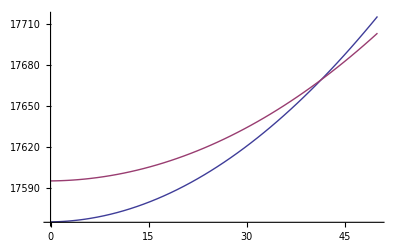

```mathematica
Plot[{TeB1Pi+Term[YB1PiNa39K,9,J],Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,32,J]},{J,0,50}]
```

#### Perturbation of B1Pi v=10 and c3Σ+ v=33, centered around J=33

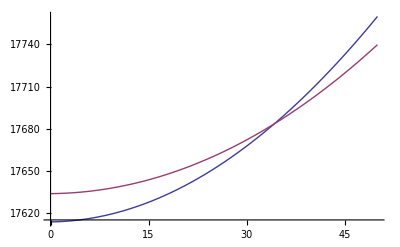

```mathematica
Plot[{TeB1Pi+Term[YB1PiNa39K,10,J],Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,33,J]},{J,0,50}]
```

#### Perturbation of B1Pi v=11 and c3Σ+ v=34, centered around J=25

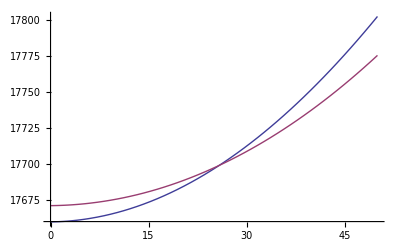

```mathematica
Plot[{TeB1Pi+Term[YB1PiNa39K,11,J],Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,34,J]},{J,0,50}]
```

#### Perturbation of B1Pi v=12 and c3Σ+ v=35, centered around J=14

```mathematica
Plot[{TeB1Pi+Term[YB1PiNa39K,12,J],Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,35,J]},{J,0,50}]
```

-Graphics-

#### Perturbation in Na41K of B1Pi v=5 and c3Σ+ v=27, centered around J=39

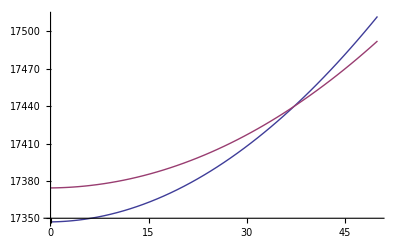

```mathematica
Plot[{TeB1Pi+Term[YB1PiNa41K,5,J],Tec3sigmaplus+Term[Yc3SigmaPlusNa41K,27,J]},{J,0,50}]
```

#### Perturbation in Na41K of B1Pi v=6 and c3Σ+ v=28, centered around J=26

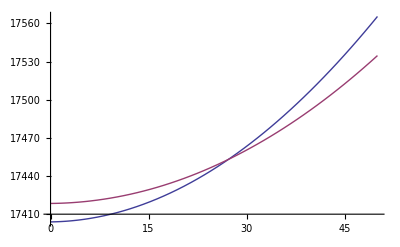

```mathematica
Plot[{TeB1Pi+Term[YB1PiNa41K,6,J],Tec3sigmaplus+Term[Yc3SigmaPlusNa41K,28,J]},{J,0,50}]
```

#### Perturbation in Na41K of B1Pi v=7 and c3Σ+ v=29, centered around J=12 and c3Σ+ v=30, centered around J=48

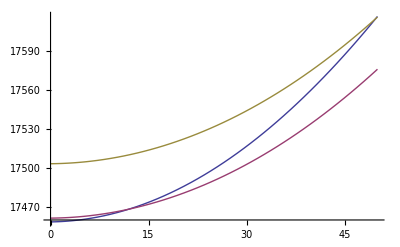

```mathematica
Plot[{TeB1Pi+Term[YB1PiNa41K,7,J],Tec3sigmaplus+Term[Yc3SigmaPlusNa41K,29,J],Tec3sigmaplus+Term[Yc3SigmaPlusNa41K,30,J]},{J,0,50}]
```

#### Perturbation in Na41K of B1Pi v=8 and c3Σ+ v=31, centered around J=42

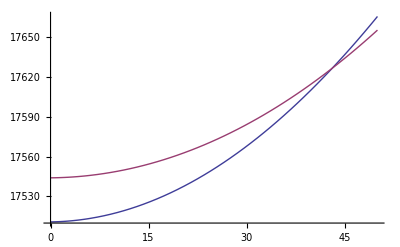

```mathematica
Plot[{TeB1Pi+Term[YB1PiNa41K,8,J],Tec3sigmaplus+Term[Yc3SigmaPlusNa41K,31,J]},{J,0,50}]
```

#### Perturbation in Na41K of B1Pi v=5 and c3Σ+ v=27, and b3Π v=60

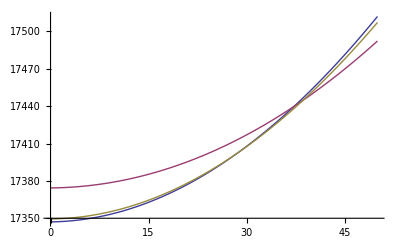

```mathematica
Plot[{TeB1Pi+Term[YB1PiNa41K,5,J],Tec3sigmaplus+Term[Yc3SigmaPlusNa41K,27,J],Teb3Pi+Term[Yb3PiNa41K,60,J]},{J,0,50}]
```

#### Perturbation in Na40K of B1Pi v=4 and c3Σ+ v=25: The states don’t cross, but are very close (0.9 cm^(-1)) to each other -> strong spin-orbit mixing expected!

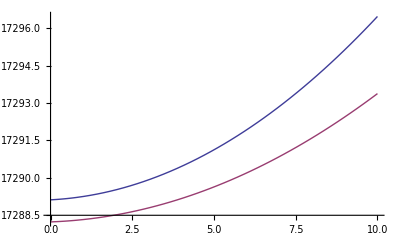

```mathematica
Plot[{TeB1Pi+Term[YB1PiNa40K,4,J],Tec3sigmaplus+Term[Yc3SigmaPlusNa40K,25,J]},{J,0,10}]
```

### Summary of perturbations in Na39K B1Π and c3Σ+ and b3Π: Includes Barrow et al., Can. J. Phys. 65, 1986

```mathematica
PerturbationsNa39K = {{0,26},{0,53},{0,69},{1,0},{1,47},{1,64},{1,79},{2,39},{2,60.5},{2,75},{3,29},{3,54},{3,70},{4,13},{4,48},{4,67},{5,41},{5,62},{5,76},{6,33},{6,57},{6,72},{7,23},{7,52},{7,68},{8,0},{8,46},{8,64},{8,78},{9,40},{9,60},{9,75},{10,33},{10,55},{10,71},{11,25},{11,52},{11,67.5},{11,79.5},{12,13.8},{12,47.5},{12,64.3},{12,77},{13,43},{13,61},{13,74},{14,38},{14,57.8},{14,70.8},{8,5}};
PerturbationListNa39K = Table[{PerturbationsNa39K[[i,2]],TeB1Pi+Term[YB1PiNa39K,PerturbationsNa39K[[i,1]],PerturbationsNa39K[[i,2]]]},{i,1,Dimensions[PerturbationsNa39K][[1]]}];
```

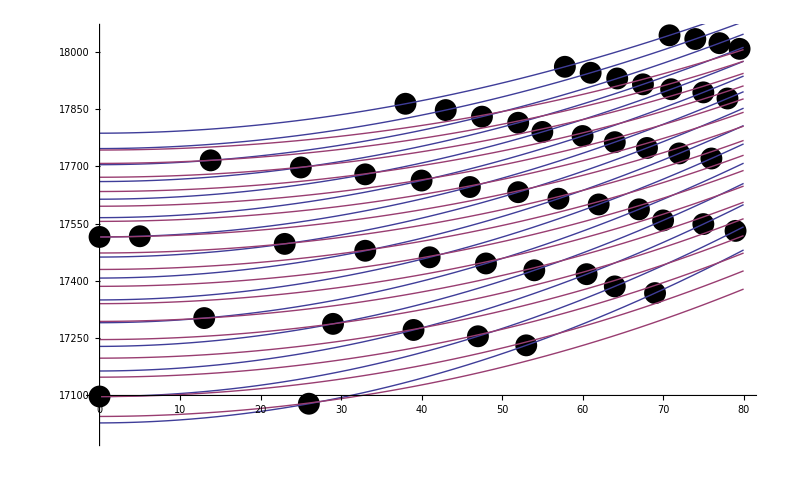

```mathematica
Show[ListPlot[PerturbationListNa39K,PlotStyle->{PointSize[0.02],Black}],Plot[{Table[TeB1Pi+Term[YB1PiNa39K,v,J],{v,0,14}],Table[Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,v,J],{v,20,36}],
Table[0*Teb3Pi+Term[Yb3PiNa39K,v,J],{v,60,66}]},{J,0,80}],PlotRange->{{0,80},{16990,18050}}]
```

#### Plot like in Derouard, Sadeghi, J. Chem. Phys. 88, 2891 (1988):

Note: In that paper, they say that the e-level couples sqrt(2) times stronger than f-level. Need to get book by Kovacs, Rotational Structure in the Spectra of Diatomic Molecules (Adam Hilder, LTD, London, 1969), and Lefebvre-Brion and R.W. Field, Perturbations in the spectra of diatomic molecules (Academic, London, 1969);

```mathematica
FoundLines[[27]]
```

-804.556

```mathematica
FoundLinesList=Table[{0,WavenumberFoundLinesAbs[[v]]},{v,1,Length[WavenumberFoundLinesAbs]}]
```

{{0,18220.9},{0,18211.1},{0,18187.5},{0,18173.7},{0,18143.4},{0,18126.3},{0,18097.},{0,18069.2},{0,18047.},{0,18024.7},{0,18001.8},{0,18000.3},{0,17975.7},{0,17950.},{0,17922.6},{0,17916.3},{0,17894.9},{0,17865.4},{0,17834.7},{0,17834.1},{0,17770.6},{0,17770.4},{0,17770.2},{0,17770.},{0,17736.5},{0,17736.3},{0,17702.8},{0,17702.6},{0,17702.1},{0,17604.6},{0,17563.1},{0,17504.7},{0,17473.1},{0,17467.3},{0,17467.1},{0,17466.4},{0,17466.3},{0,17334.6},{0,17333.1},{0,17286.8},{0,17237.9},{0,17191.3}}

ListPlot::lpn: PerturbationListNa39Kvsx is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in ….

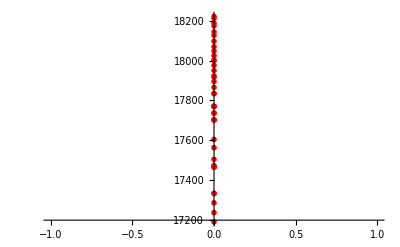
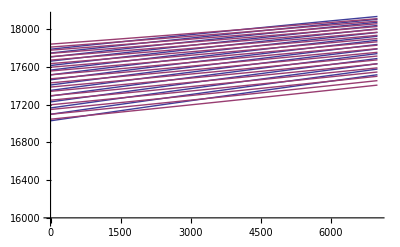
Show[-Graphics-,ListPlot[PerturbationListNa39Kvsx,PlotStyle→{PointSize[0.02],GrayLevel[0]}],-Graphics-,PlotRange→{{0,7000},{16990,18050}}]

```mathematica
Show[ListPlot[FoundLinesList,PlotStyle->{PointSize[0.01],Red}],ListPlot[PerturbationListNa39Kvsx,PlotStyle->{PointSize[0.02],Black}],Plot[{Table[TeB1Pi+Term[YB1PiNa39K,v,1/2 (-1+√(1+4 x))],{v,0,14}],Table[Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,v,1/2 (-1+√(1+4 x))],{v,20,39}],
Table[0*Teb3Pi+Term[Yb3PiNa39K,v,1/2 (-1+√(1+4 x))],{v,60,66}]},{x,0,7000}],PlotRange->{{0,7000},{16990,18050}}]
```

```mathematica
Derouardc3sigmaPlus=Table[{n+10,17046.01+52.43*n-0.556*n^2},{n,0,19}]
```

{{10,17046.},{11,17097.9},{12,17148.6},{13,17198.3},{14,17246.8},{15,17294.3},{16,17340.6},{17,17385.8},{18,17429.9},{19,17472.8},{20,17514.7},{21,17555.5},{22,17595.1},{23,17633.6},{24,17671.1},{25,17707.4},{26,17742.6},{27,17776.6},{28,17809.6},{29,17841.5}}

```mathematica
c3sigmaPlus=Table[{v,Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,v,0]},{v,20,39}]
```

{{20,17045.1},{21,17097.},{22,17147.9},{23,17197.6},{24,17246.3},{25,17293.8},{26,17340.3},{27,17385.6},{28,17429.8},{29,17472.8},{30,17514.8},{31,17555.6},{32,17595.2},{33,17633.7},{34,17671.1},{35,17707.2},{36,17742.3},{37,17776.1},{38,17808.7},{39,17840.2}}

```mathematica
Diffc3sigmaPlus=Table[{n,17046.01+52.43*n-0.556*n^2-(Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,n+20,0])},{n,0,19}]
```

{{0,0.926934},{1,0.868274},{2,0.784699},{3,0.682107},{4,0.56639},{5,0.443445},{6,0.319167},{7,0.199449},{8,0.0901873},{9,-0.0027234},{10,-0.0733883},{11,-0.115912},{12,-0.124401},{13,-0.0929587},{14,-0.0156911},{15,0.113297},{16,0.2999},{17,0.550014},{18,0.869532},{19,1.26435}}

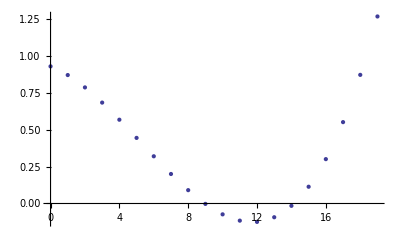

```mathematica
ListPlot[Diffc3sigmaPlus]
```

ListPlot::lpn: PerturbationListNa39Kvsx is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in ….

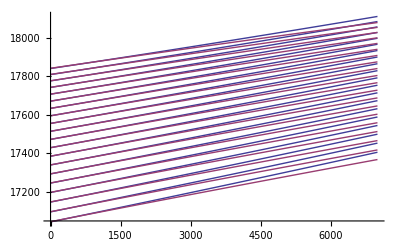
Show[ListPlot[PerturbationListNa39Kvsx,PlotStyle→{PointSize[0.02],GrayLevel[0]}],-Graphics-,PlotRange→{{0,7000},{16990,18050}}]

```mathematica
Show[ListPlot[PerturbationListNa39Kvsx,PlotStyle->{PointSize[0.02],Black}],Plot[{Table[Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,v,1/2 (-1+√(1+4 x))],{v,20,39}],
Table[17046.01+52.43*n-0.556*n^2+(0.0475 +-2.8 10^-4 n-1.9 10^-5 n^2 )x-2.07 10^-7 x^2,{n,0,19}]},{x,0,7000}],PlotRange->{{0,7000},{16990,18050}}]
```

#### Same for Na40K:

ListPlot::lpn: PerturbationListNa39Kvsx is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in ….

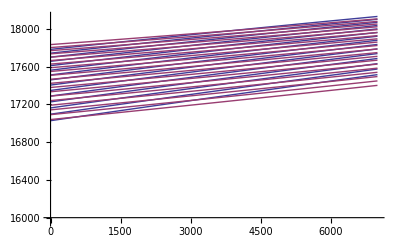
Show[ListPlot[PerturbationListNa39Kvsx,PlotStyle→{PointSize[0.02],GrayLevel[0]}],-Graphics-,-Graphics-,PlotRange→{{0,7000},{16990,18050}}]

```mathematica
Show[ListPlot[PerturbationListNa39Kvsx,PlotStyle->{PointSize[0.02],Black}],ListPlot[FoundLinesList,PlotStyle->{PointSize[0.01],Red}],Plot[{Table[TeB1Pi+Term[YB1PiNa40K,v,1/2 (-1+√(1+4 x))],{v,0,14}],Table[Tec3sigmaplus+Term[Yc3SigmaPlusNa40K,v,1/2 (-1+√(1+4 x))],{v,20,39}],
Table[0*Teb3Pi+Term[Yb3PiNa40K,v,1/2 (-1+√(1+4 x))],{v,60,66}]},{x,0,7000}],PlotRange->{{0,7000},{16990,18050}}]
```

ListPlot::lpn: PerturbationListNa39Kvsx is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in ….

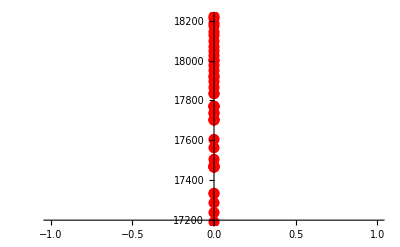
Show[ListPlot[PerturbationListNa39Kvsx,PlotStyle→{PointSize[0.02],GrayLevel[0]}],-Graphics-,-Graphics-,PlotRange→{{0,500},{17250,17350}}]

```mathematica
Show[ListPlot[PerturbationListNa39Kvsx,PlotStyle->{PointSize[0.02],Black}],ListPlot[FoundLinesList,PlotStyle->{PointSize[0.02],Red}],Plot[{Table[TeB1Pi+Term[YB1PiNa40K,v,1/2 (-1+√(1+4 x))],{v,0,14}],Table[Tec3sigmaplus+Term[Yc3SigmaPlusNa40K,v,1/2 (-1+√(1+4 x))],{v,20,39}],
Table[0*Teb3Pi+Term[Yb3PiNa40K,v,1/2 (-1+√(1+4 x))],{v,60,66}]},{x,0,7000}],PlotRange->{{0,500},{17250,17350}}]
```

```mathematica
FoundLinesList[[40]]
```

{0,17286.8}

```mathematica
Tec3sigmaplus+Term[Yc3SigmaPlusNa40K,25,0]
```

17288.2

```mathematica
Tec3sigmaplus+Term[Yc3SigmaPlusNa40K,25,0]-FoundLinesList[[40]][[2]]
```

1.44763

```mathematica
1.45*100*c/10^9
```

43.4699

```mathematica
TeB1Pi+Term[YB1PiNa40K,4,0]
```

17289.1

```mathematica
TeB1Pi+Term[YB1PiNa40K,4,0]-FoundLinesList[[40]][[2]]
```

2.33228

### Laser lines used for excitation in Ferber et al., J. Chem. Phys. 112, 5740 (2000)

Ground state:

```mathematica
De0
```

5211.75

```mathematica
DeX-IPAPotX1Na39K[[2,2]]
```

5211.76

```mathematica
DeX-BoundstatesX1Na39K[[1,2]]
```

5211.76

```mathematica
DeX-Term[YX1Na39K,0,0]
```

5211.76

B1π v=4 Je=13~ c3Σ+ v=25,Je=13 - X1Σ+ v=0 J=0:

```mathematica
TeB1Pi+Term[YB1PiNa39K,4,13]-Term[YX1Na39K,0,14]
```

17220.7

Used: 17220.4705
Diff:

```mathematica
TeB1Pi+Term[YB1PiNa39K,4,13]-Term[YX1Na39K,0,14]-17220.4705
```

0.262715

```mathematica
Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,25,13]-Term[YX1Na39K,0,14]
```

17220.5

Diff:

```mathematica
Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,25,13]-Term[YX1Na39K,0,14]-17220.4705
```

0.0164631

v=6 Jf=31~c3 v=28 N=30, Jf=31 to v=0, J=31

```mathematica
TeB1Pi+Term[YB1PiNa39K,6,31]-Term[YX1Na39K,0,31]
```

17314.6

Used: 17314.6890
Diff:

```mathematica
TeB1Pi+Term[YB1PiNa39K,6,31]-Term[YX1Na39K,0,31]-17314.6890
```

-0.119195

```mathematica
Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,28,30]-Term[YX1Na39K,0,31]
```

17315.4

```mathematica
Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,28,30]-Term[YX1Na39K,0,31]-17314.6890
```

0.747254

v=8, Je=46~v=31 Je=46 - v=0, J=45

```mathematica
TeB1Pi+Term[YB1PiNa39K,8,46]-Term[YX1Na39K,0,45]
```

17388.

Used: 17388.3084
Diff:

```mathematica
TeB1Pi+Term[YB1PiNa39K,8,46]-Term[YX1Na39K,0,45]-17388.3084
```

-0.351419

```mathematica
Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,31,46]-Term[YX1Na39K,0,45]
```

17390.8

```mathematica
Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,31,46]-Term[YX1Na39K,0,45]-17388.3084
```

2.48145

v=10, Jf=31~v=33,N=30,Jf=31 - v= 0, J=31

```mathematica
TeB1Pi+Term[YB1PiNa39K,10,31]-Term[YX1Na39K,0,31]
```

17515.3

Used: 17515.6528
Diff:

```mathematica
TeB1Pi+Term[YB1PiNa39K,10,31]-Term[YX1Na39K,0,31]-17515.6528
```

-0.364429

```mathematica
Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,33,30]-Term[YX1Na39K,0,31]
```

17516.1

```mathematica
Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,33,30]-Term[YX1Na39K,0,31]-17515.6528
```

0.473585

v=10, Jf=36 - v=0, J=36

```mathematica
TeB1Pi+Term[YB1PiNa39K,10,36]-Term[YX1Na39K,0,36]
```

17502.7

Used: 17502.0853
Diff:

```mathematica
TeB1Pi+Term[YB1PiNa39K,10,36]-Term[YX1Na39K,0,36]-17502.0853
```

0.620556

## Predictions

```mathematica
(TeB1Pi+Term[YB1PiNa40K,9,1]-DeX)*c*100/10^12+0.0017-368.43057
```

0.00482362

```mathematica
(TeB1Pi+Term[YB1PiNa40K,9,1]-Term[YX1Na40K,0,0])*c*100/10^12
```

524.687

```mathematica
(524.6870-368.43057+0.0017)*10^12/100/c
```

5212.21

```mathematica
DeX-Term[YX1Na40K,0,0]
```

5212.05

## Data from Amanda Ross

### Aime Cotton data (NaK_BX_data_these_AJR.dat)

```mathematica
TransitionsB1PiPRRoss=Import["C:\\Users\\Martin Zwierlein\\Documents\\Experiment\\NaK\\NaK stirap\\Ross data\\B1PiX1PRlines.xls"][[1]];
```

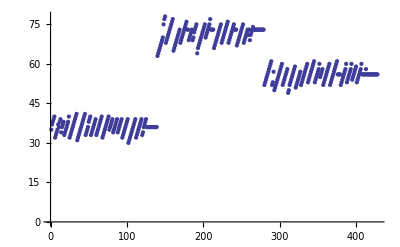

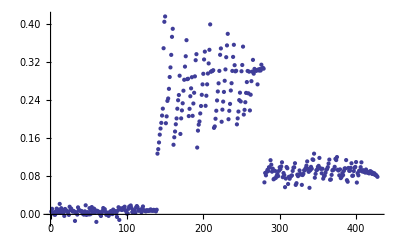

```mathematica
TransitionsB1PiPRCalc = TransitionsB1PiPRRoss;
DiffB1PiPRRoss=TransitionsB1PiPRRoss;
For[i=0,i<Dimensions[TransitionsB1PiPRRoss][[1]],i+=1;
TransitionsB1PiPRCalc[[i,1]]=TeB1Pi+Term[YB1PiNa39K,TransitionsB1PiPRRoss[[i,2]],TransitionsB1PiPRRoss[[i,5]]+TransitionsB1PiPRRoss[[i,6]]-2]-Term[YX1Na39K,TransitionsB1PiPRRoss[[i,4]],TransitionsB1PiPRRoss[[i,5]]];
DiffB1PiPRRoss[[i,1]]=TransitionsB1PiPRCalc[[i,1]]-TransitionsB1PiPRRoss[[i,1]];
];
ListPlot[DiffB1PiPRRoss[[All,3]]]
ListPlot[DiffB1PiPRRoss[[All,1]]]
```

```mathematica
TransitionsB1PiQRoss=Import["C:\\Users\\Martin Zwierlein\\Documents\\Experiment\\NaK\\NaK stirap\\Ross data\\B1PiX1Qlines.xls"][[1]];
```

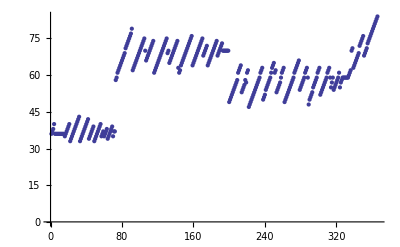

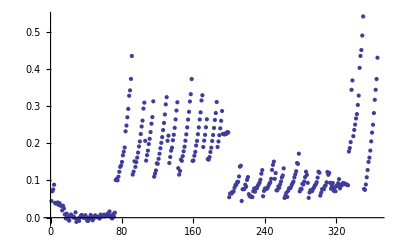

```mathematica
TransitionsB1PiQCalc = TransitionsB1PiQRoss;
DiffB1PiQRoss=TransitionsB1PiQRoss;
For[i=0,i<Dimensions[TransitionsB1PiQRoss][[1]],i+=1;
TransitionsB1PiQCalc[[i,1]]=TeB1Pi+Term[YB1PiNa39K,TransitionsB1PiQRoss[[i,2]],TransitionsB1PiQRoss[[i,5]]+TransitionsB1PiQRoss[[i,6]]-2]-Term[YX1Na39K,TransitionsB1PiQRoss[[i,4]],TransitionsB1PiQRoss[[i,5]]];
DiffB1PiQRoss[[i,1]]=TransitionsB1PiQCalc[[i,1]]-TransitionsB1PiQRoss[[i,1]];
];
ListPlot[DiffB1PiQRoss[[All,3]]]
ListPlot[DiffB1PiQRoss[[All,1]]]
```

Strange deviations. The first sequence seems to be really well reproduced, but the others have ~0.3 cm^(-1) deviation...

```mathematica
TransitionsB1PiDerou=Import["C:\\Users\\Martin Zwierlein\\Documents\\Experiment\\NaK\\NaK stirap\\Ross data\\DerouardData.xls"][[1]];
```

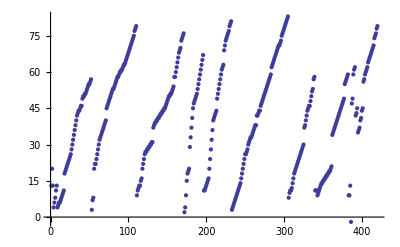

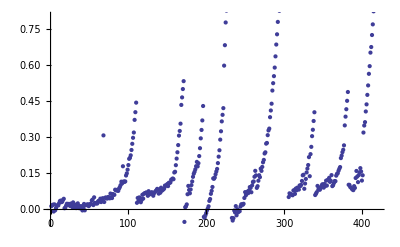

```mathematica
TransitionsB1PiDerouCalc = TransitionsB1PiDerou;
DiffB1PiDerou=TransitionsB1PiDerou;
For[i=0,i<Dimensions[TransitionsB1PiDerou][[1]],i+=1;
TransitionsB1PiDerouCalc[[i,1]]=TeB1Pi+Term[YB1PiNa39K,TransitionsB1PiDerou[[i,2]],TransitionsB1PiDerou[[i,5]]+TransitionsB1PiDerou[[i,6]]-2]-Term[YX1Na39K,TransitionsB1PiDerou[[i,4]],TransitionsB1PiDerou[[i,5]]];
DiffB1PiDerou[[i,1]]=TransitionsB1PiDerouCalc[[i,1]]-TransitionsB1PiDerou[[i,1]];
];
ListPlot[DiffB1PiDerou[[All,3]]]
ListPlot[DiffB1PiDerou[[All,1]]]
```

Apparently good to 0.05 unless we talk about large J’s...
For example, from v’=4 J=4 to v’’=4 J=5 is good to <0.02 cm^(-1) ~ 1 GHz. Great! It looks like we systematically get too large a prediction..... but ok.

```mathematica
DiffB1PiDerou[[9]]
```

{0.0179746,4.,4.,0.,5.,1.,1.}

```mathematica
TransitionsB1PiRossThesis=Import["C:\\Users\\Martin Zwierlein\\Documents\\Experiment\\NaK\\NaK stirap\\Ross data\\RossBXDataThesis.xls"][[1]];
```

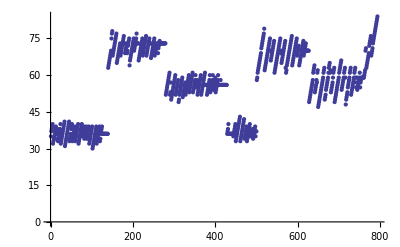

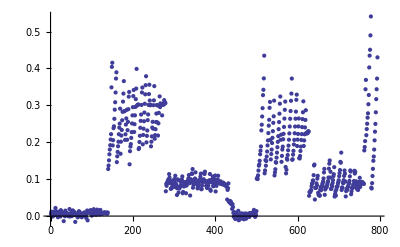

```mathematica
TransitionsB1PiRossThesisCalc = TransitionsB1PiRossThesis;
DiffB1PiRoss=TransitionsB1PiRossThesis;
For[i=0,i<Dimensions[TransitionsB1PiRossThesis][[1]],i+=1;
TransitionsB1PiRossThesisCalc[[i,1]]=TeB1Pi+Term[YB1PiNa39K,TransitionsB1PiRossThesis[[i,2]],TransitionsB1PiRossThesis[[i,5]]+TransitionsB1PiRossThesis[[i,6]]-2]-Term[YX1Na39K,TransitionsB1PiRossThesis[[i,4]],TransitionsB1PiRossThesis[[i,5]]];
DiffB1PiRoss[[i,1]]=TransitionsB1PiRossThesisCalc[[i,1]]-TransitionsB1PiRossThesis[[i,1]];
];
ListPlot[DiffB1PiRoss[[All,3]]]
ListPlot[DiffB1PiRoss[[All,1]]]
```

I guess that’s the same issue as before...

```mathematica
TransitionsBXTiemann=Import["C:\\Users\\Martin Zwierlein\\Documents\\Experiment\\NaK\\NaK stirap\\Tiemann data\\NaK_lines_X.xls"][[1]];
```

```mathematica
TransitionsBXTiemann[[1]]
```

{13768.4,24.,34.,1.,35.}

```mathematica
TeA1SigmaPlus+Term[YA1SigmaPlusNa39K,24,TransitionsBXTiemann[[1,3]]]
```

14072.5

```mathematica
TransitionsBXTiemann[[1,1]]+Term[YX1Na39K,TransitionsBXTiemann[[1,4]],TransitionsBXTiemann[[1,5]]]
```

14072.1

```mathematica
Term[YX1Na39K,TransitionsBXTiemann[[1,4]],TransitionsBXTiemann[[1,5]]]
```

303.663

CompiledFunction::cfsa: Argument $Failed at position 3 should be a "machine-size real number".

Part::pspec: Part specification 1 + k is neither an integer nor a list of integers.

Part::pspec: Part specification 1 + l is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

NSum::nsnum: Summand (or its derivative) (∑ k = 0 Dimensions[{{« 5 »}, {« 5 »}, {« 5 »}, {« 5 »}, {« 5 »}, {« 5 »}, {« 5 »}, {« 5 »}, {« 5 »}, {« 5 »}, {« 5 »}, {« 5 »}, {« 5 »}, {« 5 »}, {« 5 »}, {« 5 »}, {« 5 »}}] ⟦ 1 ⟧ - 1 {{-0.0242, 0.0952291, -2.25147×10^-7, 5.23993×10^-13, -2.85308×10^-18}, {124.009, -0.000446715, -6.93798×10^-10, 4.64013×10^-16, -2.34172×10^-19}, {-0.485187, -4.01191×10^-6, -3.84509×10^-10, 8.92977×10^-16, 3.79657×10^-20}, {-0.0032144, 3.673×10^-7, 6.70005×10^-11, -9.31093×10^-17, -3.96262×10^-21}, « 9 », {0, 0, 0, -6.63677×10^-31, 1.00225×10^-33}, {0, 0, 0, 0, -2.05836×10^-35}, {0, 0, 0, 0, 1.96939×10^-37}, {0, 0, 0, 0, -7.42126×10^-40}} ⟦ k + 1, l + 1 ⟧\ « 1 »^k)\ « 1 »^l is not numerical at point l = 1.

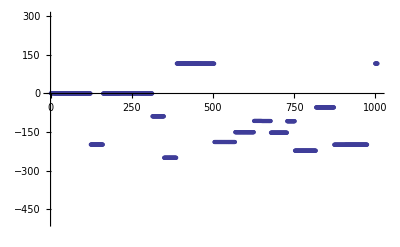

```mathematica
TransitionsBXTiemann=Import["C:\\Users\\Martin Zwierlein\\Documents\\Experiment\\NaK\\NaK stirap\\Tiemann data\\NaK_lines_X.xls"][[1]];
TransitionsBXTiemannCalc = TransitionsBXTiemann;
DiffBXTiemann=TransitionsBXTiemann;
EnergyLevelsBXTiemann=TransitionsBXTiemann;
For[i=0,i<Dimensions[TransitionsBXTiemann][[1]],i+=1;
vA1=TransitionsBXTiemann[[i,2]];
mark = TransitionsBXTiemann[[i,2]];
Which[
i<1730,TransitionsBXTiemannCalc[[i,1]]=TeA1SigmaPlus+Term[YA1SigmaPlusNa39K,TransitionsBXTiemann[[i,2]],TransitionsBXTiemann[[i,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[i,4]],TransitionsBXTiemann[[i,5]]],
i<2511,TransitionsBXTiemannCalc[[i,1]]= TeB1Pi+Term[YB1PiNa39K,TransitionsBXTiemann[[i,2]],TransitionsBXTiemann[[i,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[i,4]],TransitionsBXTiemann[[i,5]]],
mark==31,TransitionsBXTiemannCalc[[i,1]]= TeB1Pi+Term[YB1PiNa39K,10,TransitionsBXTiemann[[i,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[i,4]],TransitionsBXTiemann[[i,5]]],
mark==610,TransitionsBXTiemannCalc[[i,1]]= TeB1Pi+Term[YB1PiNa39K,10,TransitionsBXTiemann[[i,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[i,4]],TransitionsBXTiemann[[i,5]]],
mark==611,TransitionsBXTiemannCalc[[i,1]]= TeB1Pi+Term[YB1PiNa39K,12,TransitionsBXTiemann[[i,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[i,4]],TransitionsBXTiemann[[i,5]]],
mark==36,TransitionsBXTiemannCalc[[i,1]]= TeB1Pi+Term[YB1PiNa39K,10,TransitionsBXTiemann[[i,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[i,4]],TransitionsBXTiemann[[i,5]]],
mark==25,TransitionsBXTiemannCalc[[i,1]]= TeB1Pi+Term[YB1PiNa39K,10,TransitionsBXTiemann[[i,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[i,4]],TransitionsBXTiemann[[i,5]]],
mark==326,TransitionsBXTiemannCalc[[i,1]]= TeB1Pi+Term[YB1PiNa39K,10,TransitionsBXTiemann[[i,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[i,4]],TransitionsBXTiemann[[i,5]]],
mark==26,TransitionsBXTiemannCalc[[i,1]]= TeB1Pi+Term[YB1PiNa39K,10,TransitionsBXTiemann[[i,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[i,4]],TransitionsBXTiemann[[i,5]]],
True,TransitionsBXTiemannCalc[[i,1]]= TeB1Pi+Term[YB1PiNa39K,6,TransitionsBXTiemann[[i,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[i,4]],TransitionsBXTiemann[[i,5]]]
]; 
DiffBXTiemann[[i,1]]=TransitionsBXTiemannCalc[[i,1]]-TransitionsBXTiemann[[i,1]];
];
ListPlot[DiffBXTiemann[[2500;;3506,1]],PlotRange->{-500,300}]
```

```mathematica
TransitionsBXTiemann[[2510;;2700,2]]
```

{11.,31.,31.,31.,31.,31.,31.,31.,31.,31.,31.,31.,31.,31.,31.,31.,31.,31.,31.,31.,31.,31.,31.,31.,31.,31.,31.,31.,31.,31.,31.,31.,31.,31.,31.,31.,31.,31.,610.,610.,610.,610.,610.,610.,610.,610.,610.,610.,610.,610.,610.,610.,610.,610.,610.,610.,610.,610.,610.,610.,610.,610.,610.,611.,611.,611.,611.,611.,611.,611.,611.,611.,611.,611.,611.,611.,611.,611.,611.,611.,611.,36.,36.,36.,36.,36.,36.,36.,36.,36.,36.,36.,36.,36.,36.,36.,36.,36.,36.,36.,36.,36.,36.,36.,36.,36.,36.,36.,36.,36.,36.,36.,36.,37.,37.,37.,37.,37.,37.,37.,37.,37.,37.,37.,37.,37.,37.,37.,37.,37.,37.,37.,37.,37.,37.,37.,37.,37.,37.,37.,37.,37.,37.,37.,37.,37.,38.,38.,38.,38.,38.,24.,24.,24.,24.,24.,24.,24.,24.,24.,24.,24.,24.,24.,24.,24.,24.,24.,24.,24.,24.,24.,24.,24.,24.,24.,24.,24.,24.,24.,24.,24.,24.,24.,24.,24.,24.,24.,24.,24.,24.}

CompiledFunction::cfsa: Argument $Failed at position 3 should be a "machine-size real number".

Part::pspec: Part specification 1 + k is neither an integer nor a list of integers.

Part::pspec: Part specification 1 + l is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

NSum::nsnum: Summand (or its derivative) (∑ k = 0 Dimensions[{{« 5 »}, {« 5 »}, {« 5 »}, {« 5 »}, {« 5 »}, {« 5 »}, {« 5 »}, {« 5 »}, {« 5 »}, {« 5 »}, {« 5 »}, {« 5 »}, {« 5 »}, {« 5 »}, {« 5 »}, {« 5 »}, {« 5 »}}] ⟦ 1 ⟧ - 1 {{-0.0242, 0.0952291, -2.25147×10^-7, 5.23993×10^-13, -2.85308×10^-18}, {124.009, -0.000446715, -6.93798×10^-10, 4.64013×10^-16, -2.34172×10^-19}, {-0.485187, -4.01191×10^-6, -3.84509×10^-10, 8.92977×10^-16, 3.79657×10^-20}, {-0.0032144, 3.673×10^-7, 6.70005×10^-11, -9.31093×10^-17, -3.96262×10^-21}, « 9 », {0, 0, 0, -6.63677×10^-31, 1.00225×10^-33}, {0, 0, 0, 0, -2.05836×10^-35}, {0, 0, 0, 0, 1.96939×10^-37}, {0, 0, 0, 0, -7.42126×10^-40}} ⟦ k + 1, l + 1 ⟧\ « 1 »^k)\ « 1 »^l is not numerical at point l = 1.

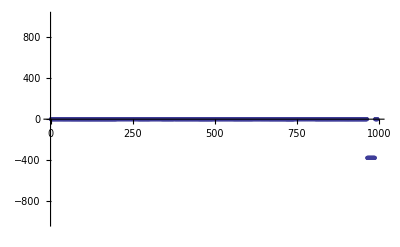

```mathematica
For[i=2511,i<3506,i+=1;
mark = TransitionsBXTiemann[[i,2]];
Which[
mark==31,TransitionsBXTiemannCalc[[i,1]]= TeB1Pi+Term[YB1PiNa39K,10,TransitionsBXTiemann[[i,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[i,4]],TransitionsBXTiemann[[i,5]]],
mark==610,TransitionsBXTiemannCalc[[i,1]]= TeB1Pi+Term[YB1PiNa39K,10,TransitionsBXTiemann[[i,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[i,4]],TransitionsBXTiemann[[i,5]]],
mark==611,TransitionsBXTiemannCalc[[i,1]]= TeB1Pi+Term[YB1PiNa39K,12,TransitionsBXTiemann[[i,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[i,4]],TransitionsBXTiemann[[i,5]]],
mark==36,TransitionsBXTiemannCalc[[i,1]]= TeB1Pi+Term[YB1PiNa39K,10,TransitionsBXTiemann[[i,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[i,4]],TransitionsBXTiemann[[i,5]]],
mark==37,TransitionsBXTiemannCalc[[i,1]]= TeB1Pi+Term[YB1PiNa39K,10,TransitionsBXTiemann[[i,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[i,4]],TransitionsBXTiemann[[i,5]]],
mark==38,TransitionsBXTiemannCalc[[i,1]]= TeB1Pi+Term[YB1PiNa39K,10,TransitionsBXTiemann[[i,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[i,4]],TransitionsBXTiemann[[i,5]]],
mark==24,TransitionsBXTiemannCalc[[i,1]]= TeB1Pi+Term[YB1PiNa39K,6,TransitionsBXTiemann[[i,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[i,4]],TransitionsBXTiemann[[i,5]]],
mark==25,TransitionsBXTiemannCalc[[i,1]]= TeB1Pi+Term[YB1PiNa39K,10,TransitionsBXTiemann[[i,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[i,4]],TransitionsBXTiemann[[i,5]]],
mark==326,TransitionsBXTiemannCalc[[i,1]]= TeB1Pi+Term[YB1PiNa39K,10,TransitionsBXTiemann[[i,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[i,4]],TransitionsBXTiemann[[i,5]]],
mark==26,TransitionsBXTiemannCalc[[i,1]]= TeB1Pi+Term[YB1PiNa39K,12,TransitionsBXTiemann[[i,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[i,4]],TransitionsBXTiemann[[i,5]]],
mark==327,TransitionsBXTiemannCalc[[i,1]]= TeB1Pi+Term[YB1PiNa39K,11,TransitionsBXTiemann[[i,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[i,4]],TransitionsBXTiemann[[i,5]]],
mark==27,TransitionsBXTiemannCalc[[i,1]]= TeB1Pi+Term[YB1PiNa39K,4,TransitionsBXTiemann[[i,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[i,4]],TransitionsBXTiemann[[i,5]]],
mark==28,TransitionsBXTiemannCalc[[i,1]]= TeB1Pi+Term[YB1PiNa39K,4,TransitionsBXTiemann[[i,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[i,4]],TransitionsBXTiemann[[i,5]]],
mark==29,TransitionsBXTiemannCalc[[i,1]]= TeB1Pi+Term[YB1PiNa39K,4,TransitionsBXTiemann[[i,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[i,4]],TransitionsBXTiemann[[i,5]]],
mark==307,TransitionsBXTiemannCalc[[i,1]]= TeB1Pi+Term[YB1PiNa39K,10,TransitionsBXTiemann[[i,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[i,4]],TransitionsBXTiemann[[i,5]]],
mark==308,TransitionsBXTiemannCalc[[i,1]]= TeB1Pi+Term[YB1PiNa39K,9,TransitionsBXTiemann[[i,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[i,4]],TransitionsBXTiemann[[i,5]]],
mark==9,TransitionsBXTiemannCalc[[i,1]]= TeB1Pi+Term[YB1PiNa39K,8,TransitionsBXTiemann[[i,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[i,4]],TransitionsBXTiemann[[i,5]]],
mark==10,TransitionsBXTiemannCalc[[i,1]]= TeB1Pi+Term[YB1PiNa39K,8,TransitionsBXTiemann[[i,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[i,4]],TransitionsBXTiemann[[i,5]]],
mark==312,TransitionsBXTiemannCalc[[i,1]]= TeB1Pi+Term[YB1PiNa39K,9,TransitionsBXTiemann[[i,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[i,4]],TransitionsBXTiemann[[i,5]]],
mark==12,TransitionsBXTiemannCalc[[i,1]]= TeB1Pi+Term[YB1PiNa39K,8,TransitionsBXTiemann[[i,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[i,4]],TransitionsBXTiemann[[i,5]]],
mark==313,TransitionsBXTiemannCalc[[i,1]]= TeB1Pi+Term[YB1PiNa39K,11,TransitionsBXTiemann[[i,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[i,4]],TransitionsBXTiemann[[i,5]]],
mark==2,TransitionsBXTiemannCalc[[i,1]]= TeB1Pi+Term[YB1PiNa39K,7,TransitionsBXTiemann[[i,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[i,4]],TransitionsBXTiemann[[i,5]]],
mark==301,TransitionsBXTiemannCalc[[i,1]]= TeB1Pi+Term[YB1PiNa39K,10,TransitionsBXTiemann[[i,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[i,4]],TransitionsBXTiemann[[i,5]]],
mark==3,TransitionsBXTiemannCalc[[i,1]]= TeB1Pi+Term[YB1PiNa39K,10,TransitionsBXTiemann[[i,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[i,4]],TransitionsBXTiemann[[i,5]]],
mark==101,TransitionsBXTiemannCalc[[i,1]]= TeB1Pi+Term[YB1PiNa39K,60,TransitionsBXTiemann[[i,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[i,4]],TransitionsBXTiemann[[i,5]]],
mark==127,TransitionsBXTiemannCalc[[i,1]]= TeB1Pi+Term[YB1PiNa39K,4,TransitionsBXTiemann[[i,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[i,4]],TransitionsBXTiemann[[i,5]]],
True,TransitionsBXTiemannCalc[[i,1]]= TeB1Pi+Term[YB1PiNa39K,6,TransitionsBXTiemann[[i,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[i,4]],TransitionsBXTiemann[[i,5]]]
];
DiffBXTiemann[[i,1]]=TransitionsBXTiemannCalc[[i,1]]-TransitionsBXTiemann[[i,1]];
];
ListPlot[DiffBXTiemann[[2511;;3506,1]],PlotRange->{-1000,1000}]
```

```mathematica
DiffBXTiemann[[2813,1]]
```

0.600037

```mathematica
If[TransitionsBXTiemann[[1,2]]==1300,1,0]
```

0

```mathematica
ListPlot[Table[TeA1SigmaPlus+Term[YA1SigmaPlusNa39K,24,TransitionsBXTiemann[[v,3]]],{v,1,1
```

```mathematica
A1levelslist = Table[TeA1SigmaPlus+Term[YA1SigmaPlusNa39K,v,0],{v,0,vmaxA1SigmaPlus}];
```

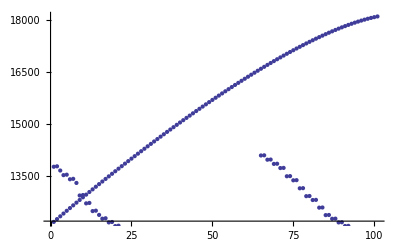

```mathematica
Show[ListPlot[A1levelslist],ListPlot[EnergyLevelsBXTiemann[[1;;1800,1]]]]
```

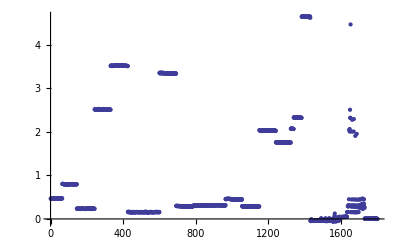

```mathematica
ListPlot[DiffBXTiemann[[1;;1800,1]]]
```

```mathematica
PerturbationsNa39K
TransitionsBXTiemann[[1,3]]
```

{{0,26},{0,53},{0,69},{1,0},{1,47},{1,64},{1,79},{2,39},{2,60.5},{2,75},{3,29},{3,54},{3,70},{4,13},{4,48},{4,67},{5,41},{5,62},{5,76},{6,33},{6,57},{6,72},{7,23},{7,52},{7,68},{8,0},{8,46},{8,64},{8,78},{9,40},{9,60},{9,75},{10,33},{10,55},{10,71},{11,25},{11,52},{11,67.5},{11,79.5},{12,13.8},{12,47.5},{12,64.3},{12,77},{13,43},{13,61},{13,74},{14,38},{14,57.8},{14,70.8},{8,5}}

34.

```mathematica
13781.396-13659.871
```

121.525

```mathematica
Term[YX1Na39K,2,33]-Term[YX1Na39K,1,33]
```

121.519

```mathematica
TeA1SigmaPlus+Term[YA1SigmaPlusNa39K,24,TransitionsBXTiemann[[1,3]]]-Term[YX1Na39K,TransitionsBXTiemann[[1,4]],TransitionsBXTiemann[[1,5]]]  - TransitionsBXTiemann[[1,1]]
```

0.465473

## Calculate bound state energies and wavefunctions

### Numerov-Cooley Integration

```mathematica
NumerovIntegration[En_,V_,cst_] := Module[{N=Dimensions[V,1][[1]],U=(V-En)*cst,i=2,j=0,Y},
Y=V;
Y[[All]]=0;
Y[[1]]=0;
cutoff=V[[N]]*cst;
While[U[[i]]>cutoff&&i≤N ,
Y[[i]]=0;
i+=1;
];
Y[[i]]=10^-10;
While[U[[i]]>0&&i<N,
Y[[i+1]]=(2+U[[i]]/(1-U[[i]]/12))*Y[[i]]-Y[[i-1]];
i+=1;
];
Yend=Y[[i]];
nturn = i;
Y[[N-1]]=0;
i=N-2;
While[U[[i]]>cutoff,
Y[[i]]=0;
i-=1;
];
Y[[i]]=10.^-10;
For[j=i+1,(j> nturn+1),j--;
Y[[j-1]]=(2+U[[j]]/(1-U[[j]]/12))Y[[j]]-Y[[j+1]];
];
scale=Y[[nturn]]/Yend;
Y[[1;;nturn-1]]*=scale;
Psi=Table[Y[[i]]/(1-U[[i]]/12),{i,1,N}];
scale = Psi.Psi;
ΔE=(-Psi[[nturn]])/(scale*cst)*((Y[[nturn-1]]+Y[[nturn+1]])-2Y[[nturn]]-U[[nturn]]*Psi[[nturn]]);
{En+ΔE,Psi/(√(scale ds))}
];
NumerovCooley[En_,V_,cst_]:=Module[{Energy},
Energy=En;
Enew=NumerovIntegration[Energy,V,cst];
While[Abs[Enew[[1]]-Energy]>.0001,
Energy=Enew[[1]];
Enew=NumerovIntegration[Energy,V,cst];
];
Enew
];
CalcEnergyPsi[V_,cst_,vmax_]:=Module[{Entab,Psitab,EnergyPsi,Energy},
Entab={};
Psitab={};
EnergyPsi={};
Energy=1;
For[i=0,i<vmax,i+=1;
EnergyPsi=NumerovCooley[Energy,V,cst];
AppendTo[Entab,{i-1,EnergyPsi[[1]]}];
AppendTo[Psitab,EnergyPsi[[2]]];
If[i>1,Energy=2*EnergyPsi[[1]]-Entab[[i-1,2]],Energy=EnergyPsi[[1]]*3];
];
{Entab,Psitab}
];
NodeCount[Psi_]:=Module[{i=1},
While[Psi[[i]]==0,i+=1];
j=Length[Psi];
While[Psi[[j]]==0,j-=1];
Nodes=0;
For[k=i-1,k<j-1,k++;
Which[
(Psi[[k]]>0)&&(Psi[[k+1]]≤0),Nodes+=1,
(Psi[[k]]≤0)&&(Psi[[k+1]]>0),Nodes+=1,
True,1];
];
Nodes];
```

### X1Σ+

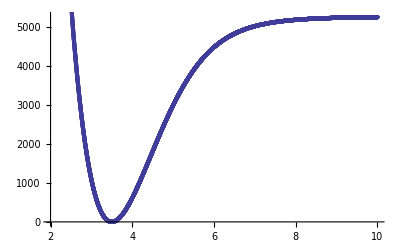

```mathematica
ds = 10^-3;
cst= (2 muNa40K*u 10^-20)/hbar^2 h c 100 ds^2;
xstart =2;
xend =10;
V={};
V=Table[UtotX1[r]+DeX,{r,xstart,xend,ds}];
xlist=Table[r,{r,xstart,xend,ds}];
ListPlot[Table[{xlist[[i]],V[[i]]},{i,1,Dimensions[xlist,1][[1]]}],PlotRange->{{2,10},{0,DeX}}]
```

```mathematica
EnergyPsitabX1=CalcEnergyPsi[V,cst,vmaxX1];
EntabX1=EnergyPsitabX1[[1]]
PsitabX1=EnergyPsitabX1[[2]];
(*Animate[ListPlot[NumerovIntegration[En][[2]],PlotRange->{-3,3}],{En,0,5000}]*)
```

{{0,61.5747},{1,184.042},{2,305.522},{3,426.007},{4,545.49},{5,663.965},{6,781.425},{7,897.863},{8,1013.27},{9,1127.64},{10,1240.96},{11,1353.22},{12,1464.42},{13,1574.53},{14,1683.55},{15,1791.47},{16,1898.27},{17,2003.95},{18,2108.48},{19,2211.84},{20,2314.04},{21,2415.04},{22,2514.84},{23,2613.41},{24,2710.74},{25,2806.81},{26,2901.59},{27,2995.07},{28,3087.22},{29,3178.02},{30,3267.44},{31,3355.46},{32,3442.05},{33,3527.19},{34,3610.84},{35,3692.96},{36,3773.54},{37,3852.54},{38,3929.91},{39,4005.63},{40,4079.65},{41,4151.93},{42,4222.44},{43,4291.13},{44,4357.94},{45,4422.84},{46,4485.78},{47,4546.69},{48,4605.54},{49,4662.26},{50,4716.79},{51,4769.08},{52,4819.06},{53,4866.68},{54,4911.86},{55,4954.54},{56,4994.67},{57,5032.16},{58,5066.97},{59,5099.03},{60,5128.29},{61,5154.7}}

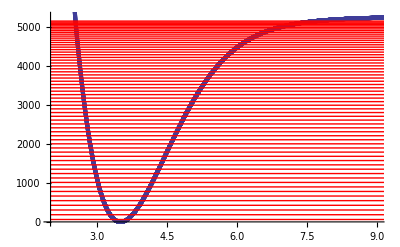

-Graphics-

```mathematica
Show[ListPlot[Table[{xlist[[i]],V[[i]]},{i,1,Dimensions[xlist,1][[1]]}],PlotRange->{{2,9},{0,DeX}}],Graphics[Table[{Directive[Red],Line[{{xstart,EntabX1[[i,2]]},{xend,EntabX1[[i,2]]}}]},{i,1,vmaxX1}]]]
ListPlot[Table[Table[{xlist[[j]],50*PsitabX1[[i,j]]+EntabX1[[i,2]]},{j,1,Length[xlist]}],{i,1,vmaxX1}],PlotRange->{0,DeX}]
NodeList=Table[{i-1,NodeCount[PsitabX1[[i]]]},{i,1,vmaxX1}];
```

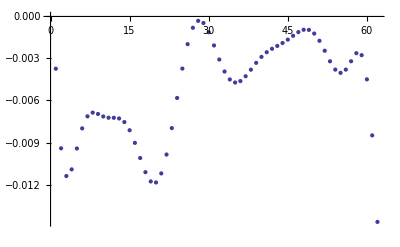

```mathematica
ListPlot[Table[{i,BoundstatesX1Na40K[[i,2]]-EntabX1[[i,2]]},{i,1,62}]]
```

### a3Σ+

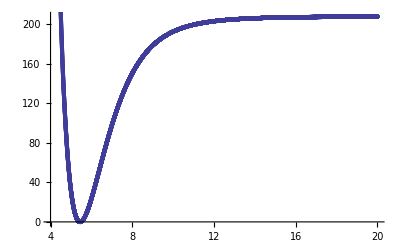

```mathematica
ds = 10^-3;
cst= (2 muNa40K*u 10^-20)/hbar^2 h c 100 ds^2;
xstart =2;
xend =20;
V=Table[Utota3[r]+Dea3,{r,xstart,xend,ds}];
xlist=Table[r,{r,xstart,xend,ds}];
ListPlot[Table[{xlist[[i]],V[[i]]},{i,1,Dimensions[xlist,1][[1]]}],PlotRange->{{4,20},{0,Dea3}}]
```

```mathematica
EnergyPsitaba3=CalcEnergyPsi[V,cst,vmaxa3];
Entaba3=EnergyPsitaba3[[1]]
Psitaba3=EnergyPsitaba3[[2]];
```

{{0,11.2123},{1,32.867},{2,53.2943},{3,72.4801},{4,90.4137},{5,107.083},{6,122.475},{7,136.577},{8,149.377},{9,160.864},{10,171.03},{11,179.87},{12,193.595},{13,207.387},{14,222.114},{15,237.516},{16,253.444},{17,280.103}}

```mathematica
ListPlot[Table[Table[{xlist[[j]],Entaba3[[1,2]]*Psitaba3[[i,j]]+Entaba3[[i,2]]},{j,1,Length[xlist]}],{i,1,12}],PlotRange->{0,Dea3}]
NodeList=Table[{i-1,NodeCount[Psitaba3[[i]]]},{i,1,vmaxa3}]
```

-Graphics-

{{0,0},{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10},{11,11},{12,13},{13,18},{14,28},{15,34},{16,39},{17,46}}

For bound state >11  there is simply some issue with guessing the good starting positions. Can be easily fixed. Cutest way would be to use WKB to guess the bound states, and use those estimates as the first attempt. The other possibility is to Plot the entire function “NumerovIntegration[En,V,cst]” For all Energies En. The zero crossings with negative slope versus Energy are the Eigenenergies:

```mathematica
NumerovList=Table[{En,NumerovIntegration[En,V,cst][[1]]-En},{En,1,Dea3,.5}];
```

$Aborted

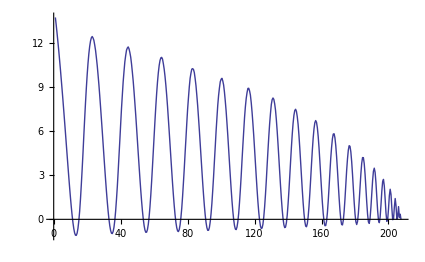

```mathematica
ListPlot[NumerovList,Joined->True]
```

So now it’s clear that we need to be careful beyond the Energy of 200.

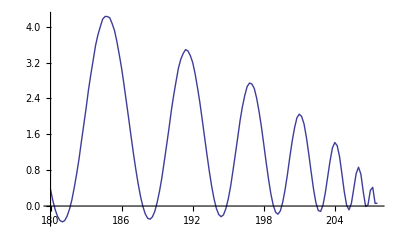

```mathematica
NumerovList2=Table[{En,NumerovIntegration[En,V,cst][[1]]-En},{En,180,Dea3,.2}];
ListPlot[NumerovList2,Joined->True]
```

The v=12 bound state energy is more like 187.8 or so. Let’s try:

```mathematica
NumerovCooley[187.8,V,cst][[1]]
```

187.786

Yes, that works. Etc...

```mathematica
DeX
```

5273.62

```mathematica
BoundstatesX1Na40K[[1,2]]
```

61.571

```mathematica
BoundstatesX1Na39K[[1,2]]-BoundstatesX1Na40K[[1,2]]
```

0.287456

### B1Π

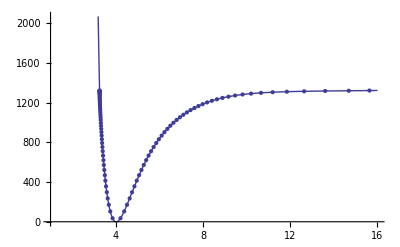

```mathematica
VB1PiNaKInterp := Interpolation[Join[Table[{RKRPotB1PiNaK39corr[[v,3]],RKRPotB1PiNaK39corr[[v,2]]},{v,1,44}],Table[{RKRPotB1PiNaK39corr[[v,4]],RKRPotB1PiNaK39corr[[v,2]]},{v,1,44}]]]
VB1PiNaK[r_] := If[r<3.251, 3.85547 10^9/r^12-1450.79,VB1PiNaKInterp[r]]
Show[Plot[VB1PiNaK[x],{x,1,16}],ListPlot[Join[Table[{RKRPotB1PiNaK39corr[[v,3]],RKRPotB1PiNaK39corr[[v,2]]},{v,1,44}],Table[{RKRPotB1PiNaK39corr[[v,4]],RKRPotB1PiNaK39corr[[v,2]]},{v,1,44}]]]]
```

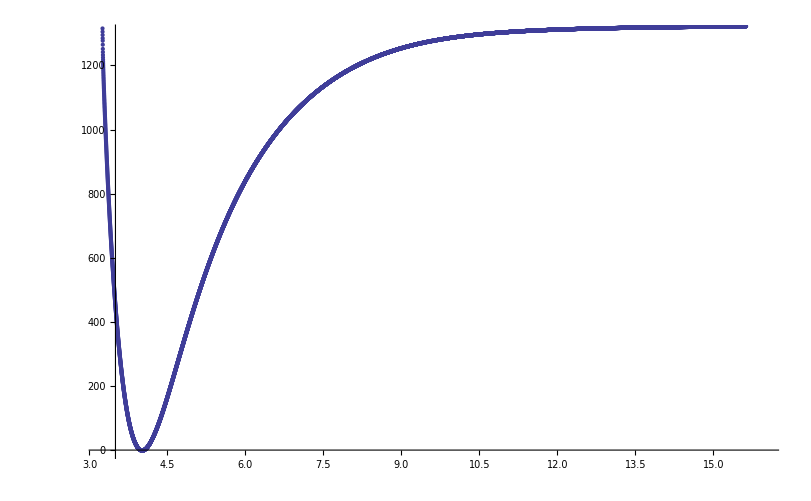

```mathematica
ds = 10^-3;
cst= (2 muNa40K*u 10^-20)/hbar^2 h c 100 ds^2;
xstart =3.251;
xend =15.63;
V=Table[VB1PiNaK[r],{r,xstart,xend,ds}];
xlist=Table[r,{r,xstart,xend,ds}];
ListPlot[Table[{xlist[[i]],V[[i]]},{i,1,Dimensions[xlist,1][[1]]}],PlotRange->{{3.25,16},{0,1300}}]
```

```mathematica
EnergyPsitabB1=CalcEnergyPsi[V,cst,];
EntabB1=EnergyPsitabB1[[1]]
PsitabB1=EnergyPsitabB1[[2]];
```

{{0,34.3999},{1,103.808},{2,170.251},{3,234.402},{4,296.17},{5,355.591},{6,412.662},{7,467.443},{8,519.982},{9,570.322},{10,618.527},{11,664.655},{12,708.765},{13,750.927},{14,791.202}}

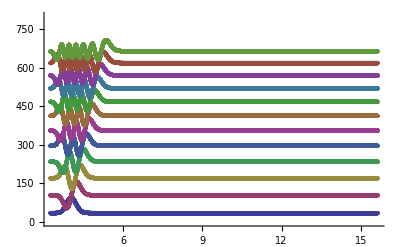

{{0,0},{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10},{11,11},{12,12},{13,13},{14,14}}

```mathematica
ListPlot[Table[Table[{xlist[[j]],EntabB1[[1,2]]*PsitabB1[[i,j]]+EntabB1[[i,2]]},{j,1,Length[xlist]}],{i,1,12}],PlotRange->{0,800}]
NodeList=Table[{i-1,NodeCount[PsitabB1[[i]]]},{i,1,15}]
```

For bound state >11  there is simply some issue with guessing the good starting positions. Can be easily fixed. Cutest way would be to use WKB to guess the bound states, and use those estimates as the first attempt. The other possibility is to Plot the entire function “NumerovIntegration[En,V,cst]” For all Energies En. The zero crossings with negative slope versus Energy are the Eigenenergies:

```mathematica
NumerovList=Table[{En,NumerovIntegration[En,V,cst][[1]]-En},{En,1,Dea3,.5}];
```

$Aborted

```mathematica
ListPlot[NumerovList,Joined->True]
```

-Graphics-

So now it’s clear that we need to be careful beyond the Energy of 200.

```mathematica
NumerovList2=Table[{En,NumerovIntegration[En,V,cst][[1]]-En},{En,180,Dea3,.2}];
ListPlot[NumerovList2,Joined->True]
```

-Graphics-

The v=12 bound state energy is more like 187.8 or so. Let’s try:

```mathematica
NumerovCooley[187.8,V,cst][[1]]
```

187.786

Yes, that works. Etc...

```mathematica
DeX
```

5273.62

```mathematica
BoundstatesX1Na40K[[1,2]]
```

61.571

```mathematica
BoundstatesX1Na39K[[1,2]]-BoundstatesX1Na40K[[1,2]]
```

0.287456